### The Interaction Potential

```mathematica
redmass=1/2;
k[en_]:=Sqrt[2*redmass*en]
wp=20;
ϵ=10^-5;
```

```mathematica
Clear[r,c1,c2,c3]
```

```mathematica
V[r_,c1_,c2_,c3_]:=c1 Exp[-r^2]-c2(1-(1+r^2/c3^2)Exp[-r^2/c3^2])^2/r^6
```

```mathematica
Manipulate[Plot[Evaluate[V[r,c1,c2,c3]],{r,0,6}],{c1,0,35,Appearance->"Labeled"},{c2,120,170,Appearance->"Labeled"},{c3,1,1.83,Appearance->"Labeled"}]
```

```mathematica
4^2
```

16

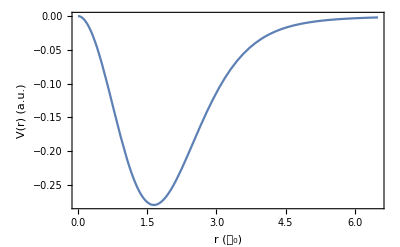

```mathematica
Plot[Evaluate[V[r,0,147,1.83]],{r,0,6.5},Frame->True,FrameLabel->{"r (𝒶_0)","V(r) (a.u.)"},FrameStyle->Directive[Medium]]
```

Wavefunction

```mathematica
s[en_,c1_,c2_,c3_]:=NDSolve[{-y''[x]/(2*redmass)+(V[SetPrecision[x,wp],SetPrecision[c1,wp],SetPrecision[c2,wp],SetPrecision[c3,wp]]-2*SetPrecision[en,wp])y[x]==0,y'[ϵ]==ϵ,y[ϵ]==0},y,{x,ϵ,300},WorkingPrecision->wp]
```

```mathematica
wfn1[x_,en_,c1_,c2_,c3_]:=y[x]/.s[en,c1,c2,c3]⟦1⟧
```

```mathematica
Manipulate[Plot[Evaluate[{wfn1[x,en,c1,c2,c3],V[x,c1,c2,c3]/50000}],{x,ϵ,300},PlotRange->{{0,50},{-0.00040,0.000100}},AxesLabel->{r,ψ}],{en,0,2},{c1,0,10,Appearance->"Labeled"},{c2,0,10000,Appearance->"Labeled"},{c3,1.83,2,Appearance->"Labeled"}]
```

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$5992,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$6019,ϵ,300} is not a machine-sized real number.

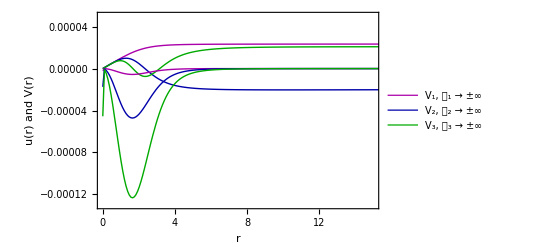

```mathematica
Plot[Evaluate[{wfn1[x,0,0,147,1.83],wfn1[x,0,0,1240,1.83],wfn1[x,0,0,3240,1.83],V[x,0,147,1.83]/50000,V[x,0,1240,1.83]/50000,V[x,0,3240,1.83]/50000}],{x,ϵ,300},PlotRange->{{0,15},{-0.00013,0.000050}},PlotStyle->{{Darker[Magenta],Thickness[0.0025]},{Darker[Blue],Thickness[0.0025]},{Darker[Green],Thickness[0.0025]},{Darker[Magenta],Thickness[0.0025]},{Darker[Blue],Thickness[0.0025]},{Darker[Green],Thickness[0.0025]}},PlotLegends->Placed[{"V_1, 𝒶_1 → ±∞ ","V_2, 𝒶_2 → ±∞ ","V_3, 𝒶_3 → ±∞ "},{Right,Bottom}],Frame->True,FrameLabel->{"r","u(r) and V(r)"},FrameTicks->{{{None},{None}},{{None},{None}}},LabelStyle->Directive[Medium]]
```

```mathematica
Plot[Evaluate[{wfn1[x,0,0,134,1.83],wfn1[x,0,0,147,1.83],wfn1[x,0,0,160,1.83]}],{x,ϵ,100},PlotRange->{{-50,100},{-0.000060,0.000100}},PlotStyle->{{Darker[Blue],Thickness[0.0025]},{Darker[Orange],Thickness[0.0025]},{Darker[Green],Thickness[0.0025]}},PlotLegends->Placed[{"𝒶 < 0","𝒶 → ±∞","𝒶 > 0"},{Left,Top}],Frame->True,FrameLabel->{"r","u(r)"},FrameTicks->{{{None},{None}},{{None},{None}}},LabelStyle->Directive[Medium]]
```

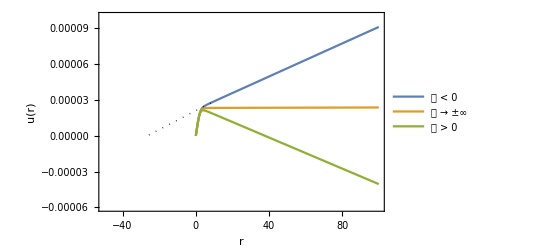

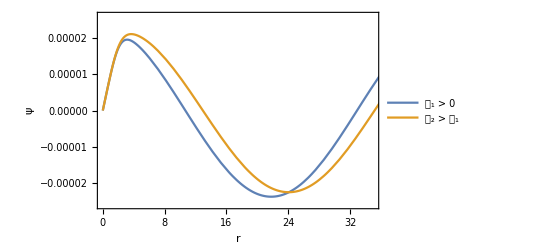

```mathematica
Plot[Evaluate[{wfn1[x,0.01,0,170,1.83],wfn1[x,0.01,0,148,1.83]}],{x,ϵ,50},PlotRange->{{0,35},{-0.000026,0.000026}},PlotLegends->Placed[{"𝒶_1 > 0","𝒶_2 > 𝒶_1"},{Right,Top}],Frame->True,FrameLabel->{r,ψ},FrameTicks->None,LabelStyle->Directive[Medium]]
```

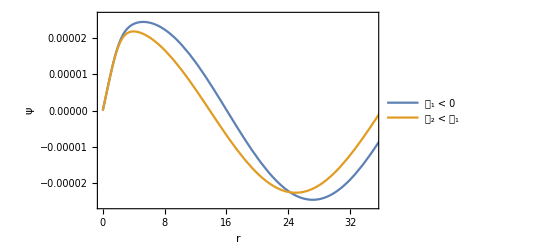

```mathematica
Plot[Evaluate[{wfn1[x,0.01,0,120,1.83],wfn1[x,0.01,0,140,1.83]}],{x,ϵ,50},PlotRange->{{0,35},{-0.000026,0.000026}},PlotLegends->Placed[{"𝒶_1 < 0","𝒶_2 < 𝒶_1"},{Right,Top}],Frame->True,FrameLabel->{r,ψ},FrameTicks->None,LabelStyle->Directive[Medium]]
```

```mathematica
xxx[x_]:=Sin[x]
```

```mathematica
posi:=Plot[Evaluate[{wfn1[x,0.01,0,180,1.83],wfn1[x,0.01,0,148,1.83],xxx[x]}],{x,ϵ,50},PlotLegends->Placed[{"𝒶_1 > 0","𝒶_2 > 𝒶_1"},{Right,Bottom}],PlotRangeFrame->True,FrameTicks->None,FrameLabel->{"r","ψ"}]
```

```mathematica
negi:=Plot[Evaluate[{wfn1[x,0.01,0,110,1.83],wfn1[x,0.01,0,140,1.83],xxx[x]}],{x,ϵ,50},PlotLegends->Placed[{"𝒶_1 < 0","𝒶_2 < 𝒶_1"},{Center,Top}],Frame->True,FrameTicks->None,FrameLabel->{"r","ψ"}]
```

Plot::optx: Unknown option PlotRangeFrame→True in Plot[«1»].

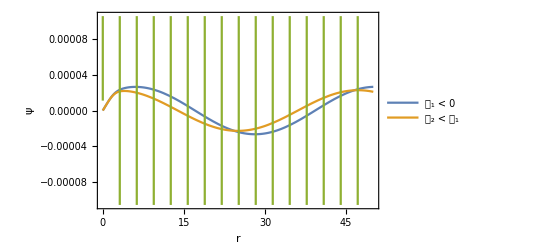

```mathematica
GraphicsRow[{negi,posi}]
```

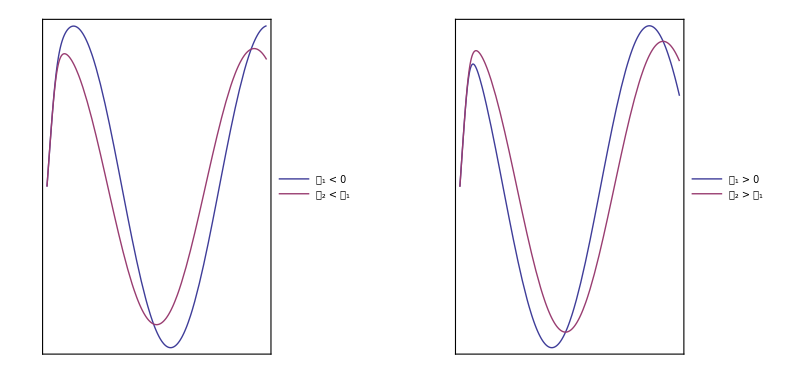

```mathematica
Clear[c1,c2,c3]
```

```mathematica
Manipulate[Plot[Evaluate[V[x,c1,c2,c3]],{x,ϵ,300},PlotRange->{{0,10},{-0.70,0.000100}},AxesLabel->{r,ψ}],{en,0,2},{c1,0,20,Appearance->"Labeled"},{c2,50,3500,Appearance->"Labeled"},{c3,2,4,Appearance->"Labeled"}]
```

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$5922,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$5963,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$6143,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$6168,ϵ,300} is not a machine-sized real number.

```mathematica
Manipulate[Plot[Evaluate[V[x,0,c2,c3]],{x,ϵ,300},PlotRange->{{0,10},{-0.30,0.000100}},AxesLabel->{r,ψ}],{en,0,2},{c2,10,200,Appearance->"Labeled"},{c3,0.1,3,Appearance->"Labeled"}]
```

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$5845,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$5870,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$6090,ϵ,300} is not a machine-sized real number.

Plot::plln: Limiting value ϵ in {Charting`Private`pvar$6115,ϵ,300} is not a machine-sized real number.

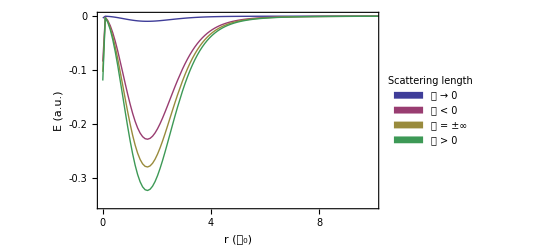

```mathematica
Plot[{V[x,0,5,1.83],V[x,0,120,1.83],V[x,0,147.07,1.83],V[x,0,170,1.83]},{x,ϵ,300},PlotRange->{{0,10},{-0.35,0.000100}},PlotLegends->SwatchLegend[{"𝒶 → 0","𝒶 < 0","𝒶 = ±∞","𝒶 > 0"},LegendLabel->"Scattering length",LegendFunction->(Framed[#]&)],Frame->True,FrameLabel->{"r (𝒶_0)","E (a.u.)"},FrameTicks->{{{-0.3,-0.2,-0.1,0},{None}},{{0,2,4,6,8,10},{None}}},LabelStyle->Directive[Medium]]
```

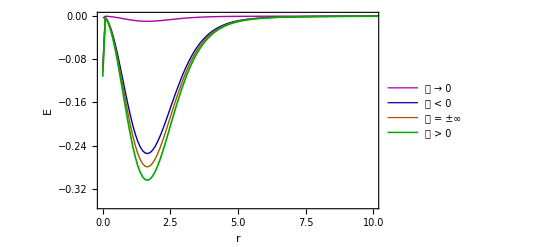

```mathematica
Plot[{V[x,0,5,1.83],V[x,0,134,1.83],V[x,0,147,1.83],V[x,0,160,1.83]},{x,ϵ,300},PlotRange->{{0,10},{-0.35,0.000100}},PlotStyle->{{Darker[Magenta],Thickness[0.0025]},{Darker[Blue],Thickness[0.0025]},{Darker[Orange],Thickness[0.0025]},{Darker[Green],Thickness[0.003]}},PlotLegends->Placed[{"𝒶 → 0","𝒶 < 0","𝒶 = ±∞","𝒶 > 0"},{Right,Top}],Frame->True,FrameLabel->{"r","E"},FrameTicks->{{{None},{None}},{{None},{None}}},LabelStyle->Directive[Medium]]
```

```mathematica
FrameTicks
```

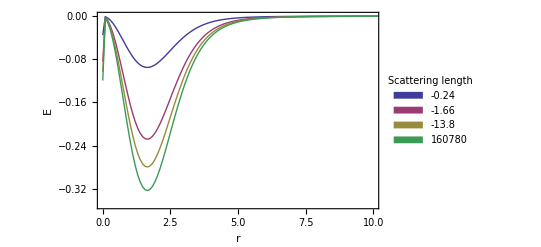

### Parameter values and potential energy minimum of the interaction potential

```mathematica
Clear[c1,c2,c3,a,wfnd]
```

```mathematica
c1=SetPrecision[0,wp];
c2=SetPrecision[147,wp];
c3=SetPrecision[1.83,wp];

FindMinimum[V[r,c1,c2,c3],{r,0.9}]
```

{-0.279491,{r→1.6439}}

```mathematica
wfnd[x_,en_,c1_,c2_,c3_]:=D[wfn1[x,en,c1,c2,c3],x];

kvot[x_,c1_,c2_,c3_]:=wfnd[x,0,c1,c2,c3]/wfn1[x,0,c1,c2,c3];
```

### Scattering length

```mathematica
a[x_,c1_,c2_,c3_]:=x-1/kvot[x,c1,c2,c3]

FindMinimum[a[x,c1,c2,c3],{x,50,400}]
```

InterpolatingFunction::dmval: Input value {367.564} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {563.83} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{-1.35254×10^11,{x→1062.47}}

```mathematica
rvdw=FindMinimum[a[x,c1,c2,c3],{x,200,400}]/1.2
```

{-4416.5,{0.833333 (x→215.313)}}

```mathematica
Manipulate[Plot[Evaluate[a[x,c1,c2,c3]],{x,0,5000},PlotLabel->"Scattering Length",AxesLabel->{r,"Scattering Length"}],{c1,0,15,Appearance->"Labeled"},{c2,147,3500,Appearance->"Labeled"},{c3,1.83,2.09,Appearance->"Labeled"}]
```

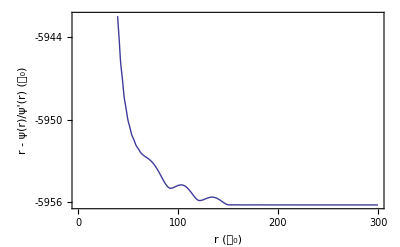

```mathematica
Plot[Evaluate[a[x,c1,c2,c3]],{x,ϵ,300},LabelStyle->Directive[Medium],Frame->True,FrameTicks->{{{-5956,-5950,-5944},None},{{0,100,200,300},None}},FrameLabel->{"r (𝒶_0)","r - ψ(r)/ψ'(r) (𝒶_0)"},FrameStyle->Directive[Medium]]
```

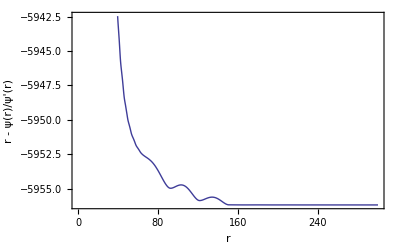

-Graphics-

### Derivative of wavefunction

```mathematica
Clear[c1,c2,c3]
```

```mathematica
c1=SetPrecision[30.868,wp];
c2=SetPrecision[100,wp];
c3=SetPrecision[1,wp];
```

```mathematica
Manipulate[Plot[Evaluate[wfnd[x,en,c1,c2,c3]],{x,ϵ,100},PlotRange->{{0,100},{-0.00007,0.00004}},AxesLabel->{r,ψ'}],{en,0,2}]
```

ReplaceAll::reps: {0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.00205286 is not a valid variable.

ReplaceAll::reps: {0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 0.00205286 is not a valid variable.

General::ivar: 2.04287 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

### Log-derivative of wavefunction

```mathematica
χ[x_,en_]:=wfnd[x,en,c1,c2,c3]/wfn1[x,en,c1,c2,c3]/k[en]
```

```mathematica
Manipulate[Plot[Evaluate[χ[x,en]],{x,ϵ,100},PlotRange->{{0,10},{-1000,1000}},AxesLabel->{r,ψ'/ψk}],{en,ϵ,2}]
```

Plot::plln: Limiting value ϵ in {x, ϵ, 100} is not a machine-sized real number.

ReplaceAll::reps: {1/100000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 0.00205286 is not a valid variable.

General::ivar: 2.04287 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

### Tangens of phase shift

```mathematica
tanδ[x_,en_]:=(1-χ[x,en]*Tan[k[en]*x])/(χ[x,en]+Tan[k[en]*x])

Manipulate[Plot[Evaluate[tanδ[x,en]],{x,ϵ,100},PlotRange->{{0,100},{-Pi,0.5}},AxesLabel->{r,"tan δ"}],{en,ϵ,1}]
```

ReplaceAll::reps: {1/100000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 0.00205286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

### Scattering length

```mathematica
tanδtab={};

Do[tr[x_]=Evaluate[tanδ[x,e0]];AppendTo[tanδtab,{e0,tr[100]}],{e0,0.0000001,0.000001,0.0000001}]

atab:=Table[{tanδtab⟦i,1⟧,-tanδtab⟦i,2⟧/k[tanδtab⟦i,1⟧]},{i,Length[tanδtab]}]
```

```mathematica
atab
```

{{1.×10^-7,408.197},{2.×10^-7,408.235},{3.×10^-7,408.254},{4.×10^-7,408.285},{5.×10^-7,408.317},{6.×10^-7,408.352},{7.×10^-7,408.376},{8.×10^-7,408.41},{9.×10^-7,408.436},{1.×10^-6,408.466}}

```mathematica
tanδtab
```

{{1.×10^-7,-0.129083},{2.×10^-7,-0.182568},{3.×10^-7,-0.22361},{4.×10^-7,-0.258222},{5.×10^-7,-0.288724},{6.×10^-7,-0.316308},{7.×10^-7,-0.341672},{8.×10^-7,-0.365293},{9.×10^-7,-0.387477},{1.×10^-6,-0.408466}}

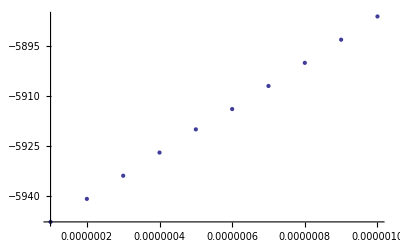

```mathematica
ListPlot[atab,PlotRange->"Automatic"]
```

### Lowest 3-body energy vs. the inverse of the scattering length

```mathematica
st=Import["/Users/kkm/Documents/Efimov_states3.xlsx"];
```

```mathematica
st⟦1⟧//Grid
```

En 3b | 1/a
-0.000261 | 0.0152332
-0.000627 | 0.00742352
-7.53384 | -0.00225793
-8.84888 | 0.00204394
-8.37021 | 0.000942285
-0.00345 | 0.00242538
-11.5035 | 0.00616371
-11.4971 | -0.000316221
-27.9404 | 0.00587889
-8.34373 | -0.0154511
-8.51801 | -0.000455612
-8.10411 | 0.0000442257
-68.5865 | 0.000336066
-8.09397 | -0.00289287
-30.0039 | 0.00404998
-29.7766 | -0.00254222
-25.2923 | -0.00199302
-6.88874 | -0.000203886
-7.13064 | -0.00173104
-0.0000301 | -0.000434013
-29.2709 | -0.0088379
-7.63402 | -0.00122291
-254.617 | -0.000408859
-24.9895 | -0.00639791
-7.55666 | -0.0319366
-7.55666 | -0.0319366
-7.79825 | -0.00266877
-7.56882 | -0.00419148
-7.25979 | 0.00177989
-6.97978 | -0.00382395
-6.44704 | -0.000777109
-22.4535 | -0.00461382
-7.65455 | -0.00468674
-28.1738 | -0.00820971
-87.7655 | -0.0036859
-30.8597 | -0.000902739
-7.99493 | 0.0052353

```mathematica
First[%1093];
```

```mathematica
Reverse/@%1094;
```

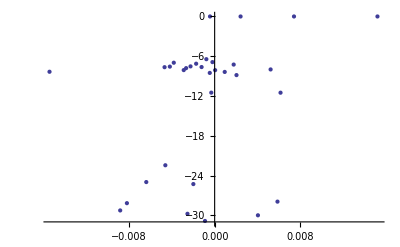

```mathematica
ListPlot[Reverse/@%1094,PlotRange->{-31,0}]
```

### Efimov states energy vs. scatteringlength when increasing parameter cw

```mathematica
sv=Import["/Users/kkm/Documents/Efimov_states4.xlsx"];
```

```mathematica
sv⟦1⟧//Grid
```

3b | scat
-91.0866 | -4.78667
-93.0211 | -8.16025
-94.9634 | -18.9339
-96.9165 | 178.844
-98.8749 | 18.005
-100.846 | 10.0701
-102.822 | 7.22659
-104.82 | 5.75168
-106.829 | 4.84184
-108.845 | 4.21718
-110.884 | 3.75719
-112.941 | 3.40103
-115.022 | 3.11323
-117.118 | 2.87345
-119.238 | 2.66863
-121.387 | 2.48898
-123.549 | 2.32907
-125.741 | 2.18354
-127.957 | 2.04916
-130.231 | 1.92337
-132.478 | 1.80353
-134.797 | 1.68852
-137.098 | 1.57638
-139.466 | 1.46589
-141.833 | 1.3558
-144.222 | 1.24489
-146.666 | 1.13216
-149.098 | 1.0159
-151.61 | 0.894998
-135.853 | 0.768066
-137.632 | 0.633089
-139.414 | 0.487353
-142.982 | 0.153968
-160.907 | -6.05768
-162.717 | -9.46111
-164.523 | -17.9825
-166.318 | -79.9313
-167.05 | 316.8
-167.222 | 143.877
-168.132 | 39.6233
-169.958 | 17.0016
-171.746 | 11.2333

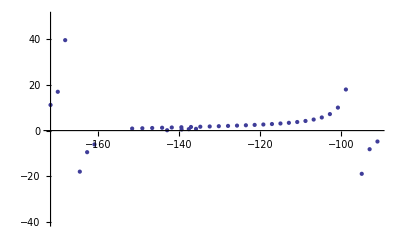

```mathematica
ListPlot[sv,PlotRange->{-40,50}]
```

### Wavefunction, gaussians

```mathematica
<<"/Users/kkm/Desktop/Efimov/wfn.nb"
```

```mathematica
wfn;

Clear[ISMAX,RSMIN,RSMAX,ILMAX,RLMIN,RLMAX,XRS,XRL,X,RATIO,f,norm]

ISMAX=25; 
RSMIN=0.01; 
RSMAX=20;
ILMAX=20; 
RLMIN=0.01; 
RLMAX=15;
```

```mathematica
XRS[1]=RSMIN;

X=Log[(RSMAX/RSMIN)]/(ISMAX-1);
RATIO=Exp[X];
XRS[J_]:=RSMIN*RATIO^(J-1)
Do[XRS[J],{J,2,ISMAX}]


XRL[1]=RLMIN

X=Log[(RLMAX/RLMIN)]/(ILMAX-1);
RATIO=Exp[X];
XRL[J_]:=RLMIN*RATIO^(J-1)
Do[XRL[J],{J,2,ILMAX}]

ii=0;
Do[ii=ii+1;
rs[ii]=XRS[i];
rl[ii]=XRL[j];
ANUE=1.0/(rs[ii]^2);
ALAM=1.0/(rl[ii]^2);
AN=2.0^4/(π)*(2*ANUE)*(2*ALAM)*Sqrt[4*ANUE*ALAM];
norm[ii]=Sqrt[AN],
{i,1,ISMAX},{j,1,ILMAX}]
```

0.01

```mathematica
imax=ISMAX ILMAX
```

500

```mathematica
rmin=0.01;
rmax=50;
```

```mathematica
f[r_,R_]=Sum[wfn⟦i,1⟧norm[i]Exp[-r^2/rs[i]^2]Exp[-R^2/rl[i]^2],{i,1,imax}];
```

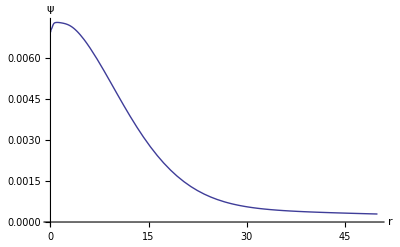

```mathematica
Plot[f[r,1],{r,rmin,rmax},AxesLabel->{"r","ψ"},LabelStyle->Directive[Medium]]
```

### Real scale

```mathematica
<<"/Users/kkm/Desktop/Efimov/output.nb"
```

```mathematica
Clear[Energy1,energy1]
```

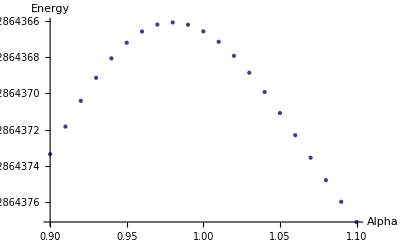

```mathematica
energy1={};

Do[fv[x_]=Evaluate[eigen[x 1.]⟦100⟧];AppendTo[energy1,fv[x]],{x,9/10,11/10,1/100}];

Energy1=Flatten[energy1];

alfa=Range[0.9,1.1,0.01];

atable=Table[{alfa⟦i⟧,Energy1⟦i⟧},{i,Length[alfa]}];

ListPlot[atable,AxesLabel->{"Alpha","Energy"}]
```

```mathematica
Export["/Users/kkm/Desktop/Efimov_results/42benergy.gif",ListPlot[atable,AxesLabel->{"Alpha","Energy"}]]
```

```mathematica
"/Users/kkm/Desktop/Efimov_results/42benergy.gif"
```

### Analytic method

### Positive scattering length

```mathematica
Clear[λ]
```

```mathematica
h[λ_]:=√(λ/2)*Cot[√λ*Pi/2]-(8/√6)*Sin[√λ*Pi/6]/Sin[√λ*Pi/2]
```

```mathematica
h1=Interpolation[Table[{Re[h[λ]],λ},{λ,-8000.01,-1.015,.1}]];
```

```mathematica
h2=Interpolation[Table[{h[λ],λ},{λ,4.01,19.91,0.01}]];
```

```mathematica
fh1[xx_]:=FindRoot[-I √λ Cos[√λ π/2]+8 I/Sqrt[3] Sin[√λ π/6]+√2 I xx Sin[√λ π/2]== 0,{λ,h1[xx]},WorkingPrecision->50]⟦1,2⟧
```

```mathematica
fh12[xx_]:=FindRoot[-I √λ Cos[√λ π/2]+8 I/Sqrt[3] Sin[√λ π/6]+√2 I xx Sin[√λ π/2]== 0,{λ,-1.02}]⟦1,2⟧
```

```mathematica
fh13[xx_]:=FindRoot[- √λ Cos[ √λ π/2]+8/Sqrt[3]  Sin[ √λ π/6]+√2 xx Sin[ √λ π/2]== 0,{λ,-2 xx^2},MaxIterations->50,WorkingPrecision->60]⟦1,2⟧
```

```mathematica
fh2[xx_]:=FindRoot[- √λ Cos[ √λ π/2]+8/Sqrt[3]  Sin[ √λ π/6]+√2 xx Sin[ √λ π/2]== 0,{λ,4.},MaxIterations->50]⟦1,2⟧
```

```mathematica
fh22[xx_]:=FindRoot[- √λ Cos[ √λ π/2]+8/Sqrt[3]  Sin[ √λ π/6]+√2 xx Sin[ √λ π/2]== 0,{λ,h2[xx]}]⟦1,2⟧
```

```mathematica
fh23[xx_]:=FindRoot[- √λ Cos[ √λ π/2]+8/Sqrt[3]  Sin[ √λ π/6]+√2 xx Sin[ √λ π/2]== 0,{λ,19.}]⟦1,2⟧
```

```mathematica
lamda[xx_]=Which[0.05<xx≤14,Re[fh1[xx]],xx<=0.05,Re[fh12[xx]],xx>14,fh13[xx]];
```

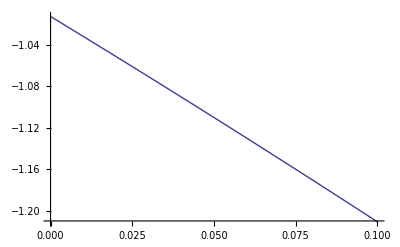

```mathematica
Plot[lamdai[x],{x,0,.1}]
```

```mathematica
lamdai=Interpolation[Join[Table[{y,lamda[y]},{y,0,1/100,1/5000}],Table[{y,lamda[y]},{y,12/1000,1/10,1/500}],Table[{y,lamda[y]},{y,11/100,1,1/100}],Table[{y,lamda[y]},{y,105/100,10,5/100}],Table[{y,lamda[y]},{y,11,500,1/10}]]]
```

InterpolatingFunction[{{0.,500.}},<>]

```mathematica
lamdai[500]
```

-500000.

```mathematica
h1
```

InterpolatingFunction[{{0.0499416,14.1423}},<>]

```mathematica
h2
```

InterpolatingFunction[{{0.,1082.05}},<>]

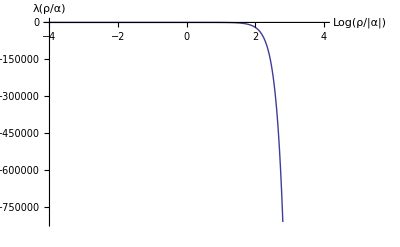

```mathematica
Plot[lamdai[10^x],{x,-4,4},AxesLabel->{"Log(ρ/|α|)","λ(ρ/α)"},AxesOrigin->{-4,0}]
```

```mathematica
lamdaex[xx_]=Which[xx>109,fh2[xx],1/100<xx<=199/100,fh22[xx],199/100<xx<201/100,21.218069818289816-5.696125887586106 xx+0.5948617583282587 xx^2,201/100<=xx<=109,fh22[xx],xx≤1/100,fh23[xx]];
```

```mathematica
lamdaexi=Interpolation[Join[Table[{y,lamdaex[y]},{y,0.0,0.01,.0002}],Table[{y,lamdaex[y]},{y,0.012,0.1,.002}],Table[{y,lamdaex[y]},{y,0.11,1.,.01}],Table[{y,lamdaex[y]},{y,1.05,100,.05}],Table[{y,lamdaex[y]},{y,100.05,4500,.5}]]];
```

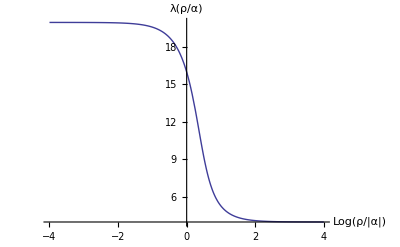

```mathematica
Plot[lamdaexi[10^x],{x,-4,4},AxesLabel->{"Log(ρ/|α|)","λ(ρ/α)"}]
```

### Negative scattering length -a

```mathematica
Clear[λ,xx]
```

```mathematica
hh[λ_]:=-√(λ/2)*Cot[√λ*Pi/2]+(8/√6)*Simplify[Sin[√λ*Pi/6]/Sin[√λ*Pi/2]]
```

```mathematica
hh1=Interpolation[Table[{Re[hh[λ]],λ},{λ,-1.01,3.9,0.1}]];
```

```mathematica
hh2=Interpolation[Table[{hh[λ],λ},{λ,0.01,7,0.01}]];
```

```mathematica
f1[xx_]:=FindRoot[-Sqrt[λ] Cos[Sqrt[λ] π/2]+8/Sqrt[3] Sin[Sqrt[λ] π/6]-Sqrt[2]*xx*Sin[Sqrt[λ] π/2]== 0,{λ,hh1[xx]},WorkingPrecision->26,AccuracyGoal->20]⟦1,2⟧
```

```mathematica
f2[xx_]:=FindRoot[-Sqrt[λ] Cos[Sqrt[λ] π/2]+8/Sqrt[3] Sin[Sqrt[λ] π/6]-Sqrt[2]*xx*Sin[Sqrt[λ] π/2]== 0,{λ,4.},AccuracyGoal->20]⟦1,2⟧
```

```mathematica
f3[xx_]:=FindRoot[-Sqrt[λ] Cos[Sqrt[λ] π/2]+8/Sqrt[3] Sin[Sqrt[λ] π/6]-Sqrt[2]*xx*Sin[Sqrt[λ] π/2]== 0,{λ,-1.},PrecisionGoal->20]⟦1,2⟧
```

```mathematica
lam[xx_]=Which[1/100<=xx<=96,f1[xx],96<xx,f2[xx],1/100>xx,Re[f3[xx]]];
```

```mathematica
lami=Interpolation[Join[Table[{y,Re[lam[y]]},{y,0,100,1/100}],Table[{y,Re[lam[y]]},{y,101,1000}],Table[{y,Re[lam[y]]},{y,1001,3000}]]]
```

InterpolatingFunction[{{0.,3000.}},<>]

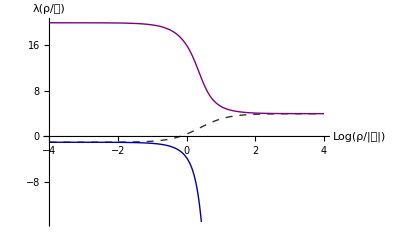

```mathematica
Plot[{lami[10^x],lamdai[10^x],lamdaexi[10^x]},{x,-4,4},AxesLabel->{"Log(ρ/|𝒶|)","λ(ρ/𝒶)"},AxesOrigin->{-4,0},PlotRange->{{-4,4},{-15,20}},PlotStyle->{Directive[GrayLevel[0.2],Dashed],Directive[Darker[Blue]],Directive[Purple]},LabelStyle->Directive[Medium]]
```

InterpolatingFunction::dmval: Input value {-3.99984} lies outside the range of data in the interpolating function. Extrapolation will be used.

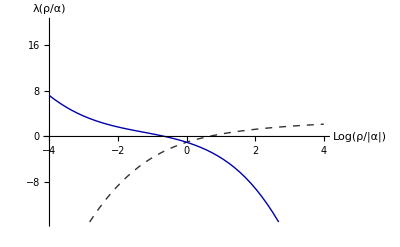

```mathematica
Plot[{lami[x],lamdai[x]},{x,-4,4},AxesLabel->{"Log(ρ/|α|)","λ(ρ/α)"},AxesOrigin->{-4,0},PlotRange->{{-4,4},{-15,20}},PlotStyle->{Directive[GrayLevel[0.2],Dashed],Directive[Darker[Blue]],Directive[Purple]},LabelStyle->Directive[Medium]]
```

```mathematica
Direct
```

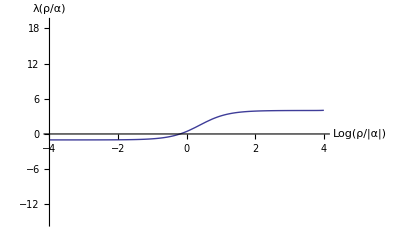

```mathematica
Plot[{lami[10^x]},{x,-4,4},AxesLabel->{"Log(ρ/|α|)","λ(ρ/α)"},AxesOrigin->{-4,0},PlotRange->{{-4,4},{-15,19}}]
```

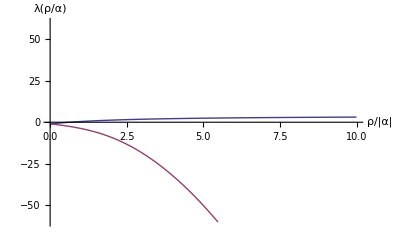

```mathematica
Plot[{lami[x],lamdai[x]},{x,0,10},AxesLabel->{"ρ/|α|","λ(ρ/α)"},PlotRange->{{0,10},{-60,60}}]
```

```mathematica
lam[10000]
```

3.99892

```mathematica
Clear[e1,a1,x,wfn3,solv4,f]
```

```mathematica
solv4[e1_,a1_]:=NDSolve[{-f''[x]+((lami[x]-1/4)/(x^2))*f[x]-a1^2*e1*f[x]==0,f'[ϵ]==ϵ,f[ϵ]==0},f,{x,ϵ,8.}]
```

```mathematica
Manipulate[Plot[Evaluate[{(lami[x/(1.7 a)]-1/4)/((x/1.7)^2),(lami[0]-1/4)/((x/1.7)^2)},{x,0,10}]],{a,-100,100}]
```

Plot::itraw: Raw object 0.326002 cannot be used as an iterator.

```mathematica
e1=1;
a1=1;
```

## Universal function, pre-calculations

```mathematica
Vn[ρ_]:=-(s0+1/4)/(ρ^2)
```

```mathematica
Vm[ρ_]:=(lami[10^ρ]-4)/(2*10^(ρ^2))
VmM[ρ_,xi_]:=(lamdai[ρ Cos[xi]]-4)/(2*ρ^2)

Vnm[ρ_,xi_]:=Which[-π<=xi<=-π/2,Vm[ρ,xi],-π/2<xi<-π/4,VmM[ρ,xi]]
```

```mathematica
Plot[Vm[.1dρ],{ρ,-4,4}]
```

-Graphics-

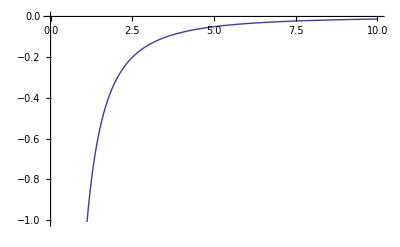

```mathematica
Plot[Vn[ρ],{ρ,0,10}]
```

```mathematica
Clear[fr3,fr4,s0,fshort,fshortp,f,xi,x,fc,fd,wwfn3,wwfn3d,wwfn4,wwfn4d,rmin,rmax]
```

```mathematica
s0=SetPrecision[1.00624,25];
```

```mathematica
fshort[x_,θ_]=Sqrt[x]*Sin[Abs[s0]*Log[x] +θ];
```

```mathematica
fshortp[x_,θ_]=D[fshort[x,θ],x];
```

```mathematica
rmin=10^-10;
rmax=5*10;
```

x=ρ lami(ρ/α) energi E=k^2

```mathematica
fr[xi_,θ_]:=NDSolve[{-f''[x]+((lami[Abs[x Cos[xi]]]-1/4)/(x^2)+2*(Sin[xi]^2)) f[x]==0,f[rmin]==fshort[rmin,θ],f'[rmin]==fshortp[rmin,θ]},f,{x,rmin,rmax},AccuracyGoal->14];
fra[xi_,θ_]:=NDSolve[{-fa''[x]+((lamdai[Abs[x Cos[xi]]]-1/4)/(x^2)+2*(Sin[xi]^2)) fa[x]==0,fa[rmin]==fshort[rmin,θ],fa'[rmin]==fshortp[rmin,θ]},fd,{x,rmin,rmax},AccuracyGoal->14]
```

```mathematica
fr3[xi_]:=NDSolve[{-fc''[x]+((lami[Abs[x Cos[xi]]]-1/4)/(x^2)+2*(Sin[xi]^2)) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.0001},fc,{x,rmax,rmin},AccuracyGoal->14]
```

```mathematica
fr4[xi_]:=NDSolve[{-fd''[x]+((lamdai[Abs[x Cos[xi]]]-1/4)/(x^2)+2*(Sin[xi]^2)) fd[x]==0,fd[rmax]==0.0,fd'[rmax]==.01},fd,{x,rmax,rmin},AccuracyGoal->14]
```

```mathematica
wwfn3[x_,xi_]:=fc[x]/.fr3[xi]⟦1⟧
```

```mathematica
wwfn3d[x_,xi_]:=fc'[x]/.fr3[xi]⟦1⟧
```

```mathematica
wwfn4[x_,xi_]:=fd[x]/.fr4[xi]⟦1⟧
```

```mathematica
wwfn4d[x_,xi_]:=fd'[x]/.fr4[xi]⟦1⟧
```

```mathematica
Clear[x,xi]
```

```mathematica
wwfn3n[x_,xi_]:=wwfn3[x,xi]/wwfn3[10 rmin,xi]fshort[10 rmin,3.09133]
```

```mathematica
wwfn3nd[x_,xi_]:=wwfn3d[x,xi]/wwfn3[10 rmin,xi] fshort[10 rmin,3.09133]
```

```mathematica
Manipulate[Plot[Evaluate[{wwfn3[x,-π/2]/wwfn3[rmin,-π/2],fshort[x,θ]/fshort[rmin,θ]}],{x,rmin,10 rmin}],{θ,0,2 π,Appearance->"Labeled"}]
```

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00018×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00018×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/10000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00018×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5219,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5279,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5403,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5431,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5512,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5539,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5677,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5704,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6194,rmin,10 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6221,rmin,10 rmin} is not a machine-sized real number.

```mathematica
Manipulate[Plot[Evaluate[{wwfn3nd[x,-π/2],fshortp[x,θ]}],{x,rmin,100 rmin}],{θ,0,2 π}]
```

Plot::plln: Limiting value rmin in {x, rmin, 100\ rmin} is not a machine-sized real number.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - 1.` SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - 1.` SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00202×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00202×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5331,rmin,100 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5366,rmin,100 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5622,rmin,100 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5649,rmin,100 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6248,rmin,100 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6275,rmin,100 rmin} is not a machine-sized real number.

```mathematica
Manipulate[Plot[Evaluate[{wwfn3n[x,-π/2],fshort[x,θ]}],{x,rmin,5 rmin}],{θ,0,2 π,Appearance->"Labeled"}]
```

Plot::plln: Limiting value rmin in {x, rmin, 5\ rmin} is not a machine-sized real number.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - 1.` SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.326002 cannot be used as a variable.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: -9.879443258836053` fc[0.32600191711901216`] - 1.` SuperscriptBox[fc[125.`] == 0.`SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00008×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {0.0001,-1.37772×10^-10 (2+0.0004 (-1/4+lami[0]))} is not a list of numbers with dimensions {2} at {x,fc[x],fc'[x]} = {50.,-1.37772×10^-10,0.0001}.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00008×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5458,rmin,5 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5485,rmin,5 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5567,rmin,5 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$5594,rmin,5 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6302,rmin,5 rmin} is not a machine-sized real number.

Plot::plln: Limiting value rmin in {Charting`Private`pvar$6329,rmin,5 rmin} is not a machine-sized real number.

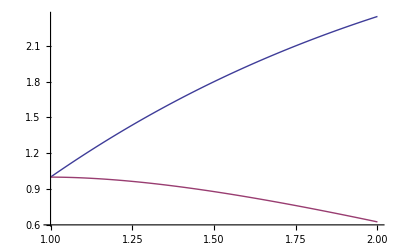

```mathematica
Plot[Evaluate[{wwfn4[x,-π]/wwfn4[rmin,-π],fshort[x,22.06668]/fshort[rmin,22.06668]}],{x,rmin,2 rmin}]
```

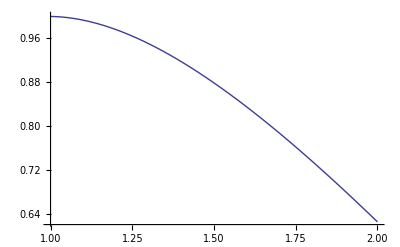

```mathematica
Plot[Evaluate[fshort[x,22.06668]/fshort[rmin,22.06668]],{x,rmin,2 rmin}]
```

### The Universal function

```mathematica
Clear[Q,Q2,Q2,Q3,Δ,xi,c,del,del2,del3]
```

```mathematica
c=3.387975056137979*10^9;
```

```mathematica
Q[xi_]:=ArcCot[(rmin wwfn3nd[rmin,xi]/wwfn3n[rmin,xi]-1/2)/Abs[s0]]-Abs[s0] Log[rmin]-21.943498251294116
```

```mathematica
Q2[xi_]:=ArcCot[(rmin wwfn4d[rmin,xi]/wwfn4[rmin,xi]-1/2)/Abs[s0]]-Abs[s0] Log[rmin]-21.943498251294116
```

```mathematica
Q3[xi_]:=ArcCot[(rmin wwfn4d[rmin,xi]/wwfn4[rmin,xi]-1/2)/Abs[s0]]-Abs[s0] Log[rmin]-π-21.943498251294116
```

```mathematica
Q[-π/2]
```

0.

```mathematica
del[xi_]:=Q[xi]*(-2)
```

```mathematica
del2[xi_]:=Q2[xi]*(-2)
```

```mathematica
del3[xi_]:=Q3[xi]*(-2)
```

```mathematica
Δ[xi_]:=Which[-π<=xi<=-π/2,del[xi],-π/2<xi<-π 3.3/8,del2[xi],-π 3.3/8<=xi<=-π/4,del3[xi]]
```

```mathematica
Δ[-π/2]
```

0.

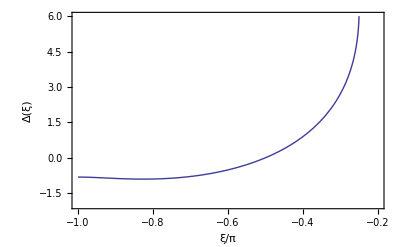

```mathematica
Plot[Evaluate[{Δ[xi π]}],{xi,-1.,-1/4},PlotRange->{{-1.,-0.2},{-2,6}},Frame->True,FrameLabel->{"ξ/π","Δ(ξ)"},FrameStyle->Directive[Medium]]
```

```mathematica
-850*0.529
```

```mathematica
-449.65000000000003/3.31
```

-135.846

```mathematica
Clear[Delta,xi,df,btable,alfa1]
```

```mathematica
Delta={};
```

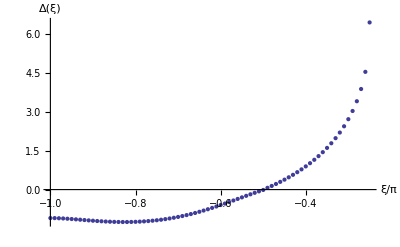

```mathematica
Do[df[xi_]=Evaluate[Δ[xi π ]];AppendTo[Delta,df[xi π]],{xi,-1,-1/4,1/100}];

alfa1=Range[-1,-1/4,1/100];

btable=Table[{alfa1⟦i⟧,Delta⟦i⟧},{i,Length[alfa1]}];

ListPlot[btable,AxesLabel->{"ξ/π","Δ(ξ)"}]
```

```mathematica
Δ[-π]
```

```mathematica
-1.09927633427567+0.89
```

-0.209276

```mathematica
6.453055365689023-6.02730678199
```

0.425749

```mathematica
Clear[gf]
```

```mathematica
gf=Interpolation[Table[{xi,Δ[xi]},{xi,-π,-π/4,π/100}]]
```

InterpolatingFunction[{{-3.14159,-0.785398}},<>]

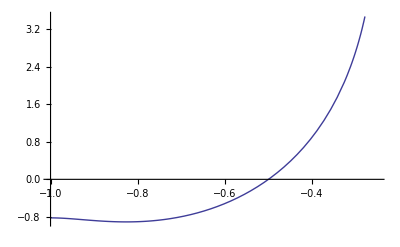

```mathematica
Plot[gf[xi π],{xi,-1,-1/4}]
```

```mathematica
gf[-π/2]
```

0.209276

#### Braatens approximative function

```mathematica
Clear[eq1,x,eq2]
```

```mathematica
eq1[xi_]:=6.04-9.63 (-π/4-xi)^(1/2)+3.10 (-π/4-xi)
```

```mathematica
eq2[xi_]:=2.12 (π/2+xi)+1.97 (π/2+xi)^2+1.17 (π/2+xi)^3
```

```mathematica
eq3[xi_]:=-0.89+0.28 ((π+xi)^2 Exp[-1/(π+xi)^2])+0.25 ((π+xi)^2 Exp[-1/(π+xi)^2])^2
```

```mathematica
Braaten[xi_]:=Which[-3 π/8<xi<=-π/4,eq1[xi],-5 π/8<=xi<=-3 π/8,eq2[xi],-π<=xi<-5 π/8,eq3[xi]]
```

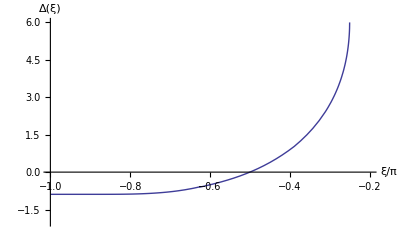

```mathematica
Plot[Braaten[xi π],{xi,-1.,-1/4},PlotRange->{{-1.,-0.2},{-2,6}},AxesLabel->{"ξ/π","Δ(ξ)"},LabelStyle->Directive[Medium]]
```

```mathematica
Plot[{Braaten[xi π],gf,{xi,-1.,-1/4},PlotRange->{{-1.,-0.2},{-2,6}},AxesLabel->{"ξ/π","Δ(ξ)"}]
```

### Analytical Efimov States

#### K=H Sin(ξ) as a function of 1/a=H Cos(ξ)

```mathematica
n=4;
n0=4;
```

```mathematica
Clear[Effi,Effi1,Effi2,H,H0,H01,H1,H2]
```

```mathematica
H02[ξ_]:=((Exp[-2 π/s0])^-3 Exp[gf[ξ]/s0])^(1/2)
```

```mathematica
H01[ξ_]:=((Exp[-2 π/s0])^-2 Exp[gf[ξ]/s0])^(1/2)
```

```mathematica
H0[ξ_]:=((Exp[-2 π/s0])^-1 Exp[gf[ξ]/s0])^(1/2)
```

```mathematica
H[ξ_]:=((Exp[-2 π/s0])^(n-n0) Exp[gf[ξ]/s0]0.029)^(1/2)
```

```mathematica
H1[ξ_]:=((Exp[-2 π/s0]) Exp[gf[ξ]/s0]*0.029)^(1/2)
```

```mathematica
H2[ξ_]:=((Exp[-2 π/s0])^2 Exp[gf[ξ]/s0]*0.029)^(1/2)
```

```mathematica
Effi=Table[{H[ξ π]^(1/4) Cos[ξ π],H[ξ π]^(1/4) Sin[ξ π]},{ξ,-1,-1/4,1/500}];
```

```mathematica
Effi1=Table[{H1[ξ π]^(1/4) Cos[ξ π],H1[ξ π]^(1/4) Sin[ξ π]},{ξ,-1,-1/4,1/500}];
```

```mathematica
Effi2=Table[{H2[ξ π]^(1/4) Cos[ξ π],H2[ξ π]^(1/4) Sin[ξ π]},{ξ,-1,-1/4,1/500}];
```

```mathematica
Effi3=Table[{H0[ξ π]^(1/4) Cos[ξ π],H0[ξ π]^(1/4) Sin[ξ π]},{ξ,-1,-1/4,1/500}];
```

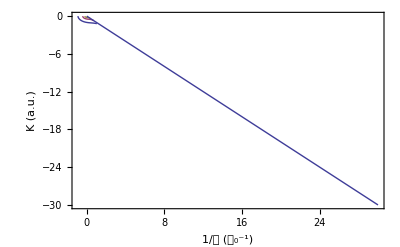

```mathematica
Show[ListLinePlot[{Effi,Effi1,Effi2},PlotRange->{{-1,1.2},{0,-1.2}},Frame->True,FrameLabel->{"1/𝒶 (𝒶_0^-1)","K (a.u.)"}],Plot[-x,{x,0,30}],LabelStyle->Directive[Medium]]
```

```mathematica
H[-π] Cos[-π]
```

-0.665486

```mathematica
N[1/(H[-π] Cos[-π])]
```

-1.50266

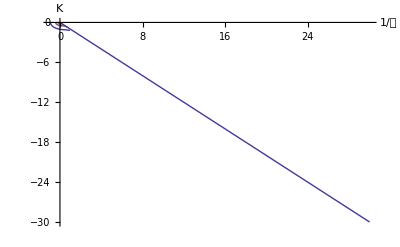

```mathematica
Show[ListLinePlot[{Effi,Effi1,Effi2},PlotRange->{{-1,1.2},{0,-1.2}},AxesLabel->{"1/𝒶","K"}],Plot[-x,{x,0,30}],LabelStyle->Directive[Medium]]
```

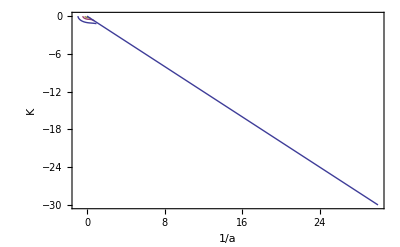

-Graphics-

```mathematica
EffiR=Table[{H[ξ π] Cos[ξ π],H[ξ π] Sin[ξ π]},{ξ,-1,-1/4,1/500}];
```

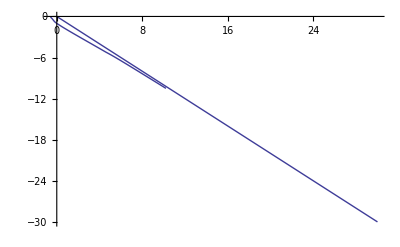

```mathematica
Show[ListLinePlot[EffiR,PlotRange->{{-2,9},{0,-10.5}}],Plot[-x,{x,0,30}]]
```

```mathematica
HB[ξ_]:=((Exp[-2 π/s0])^(n-n0) Exp[Braaten[ξ]/s0])^(1/2)
```

```mathematica
HB[-π] Cos[-π]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Indeterminate

```mathematica
Braaten[-π]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Indeterminate

```mathematica
1/(H1[-π] Cos[-π])
```

-38.9122

```mathematica
H1[-π/2]Sin[-π/2]
```

-0.0440641

```mathematica
-38.9122*0.0440641
```

-1.71463

```mathematica
-1.71463010564336*(1.662/1.74)
```

-1.63777

```mathematica
-10.06865467022413/1.6
```

-6.29291

```mathematica
r6=N[(147^(1/4))/2]
```

1.741

```mathematica
Show[ListLinePlot[{Effi,Effi1,Effi2},PlotRange->{{-1.2,1.2},{-1.2,1.2}},Axes->True,AxesStyle->Arrowheads[0.04]],Plot[-x,{x,0,30}],Graphics[{Dashed,Circle[{0,0},1]}],Graphics[{Blue,Circle[{0,0},0.6,{0,-1.2*Pi/4}],Text[Style["ξ",FontSize->18,Blue],{0.65,-0.4}]}],LabelStyle->Directive[Medium],ImageSize->{Automatic,329},AspectRatio->Automatic,AxesLabel->{"1/𝒶 (𝒶_0^-1)","K (a.u.)"}]
```

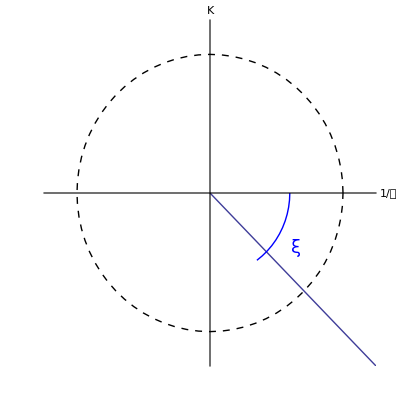

```mathematica
Show[ListLinePlot[{Effi,Effi1,Effi2},PlotRange->{{-1.2,1.2},{-1.2,1.2}},Axes->True,AxesStyle->Arrowheads[0.04]],Plot[-x,{x,0,30}],Graphics[{Dashed,Circle[{0,0},1]}],Graphics[{Blue,Circle[{0,0},0.6,{0,-1.2*Pi/4}],Text[Style["ξ",FontSize->18,Blue],{0.65,-0.4}]}],LabelStyle->Directive[Medium],ImageSize->{Automatic,329},AspectRatio->Automatic,Ticks->None]
```

```mathematica
Clear[s,threshold]
```

```mathematica
s[x_]:=-x
```

```mathematica
threshold[x_]=Which[x≤0,0,0<x,s[x]];
```

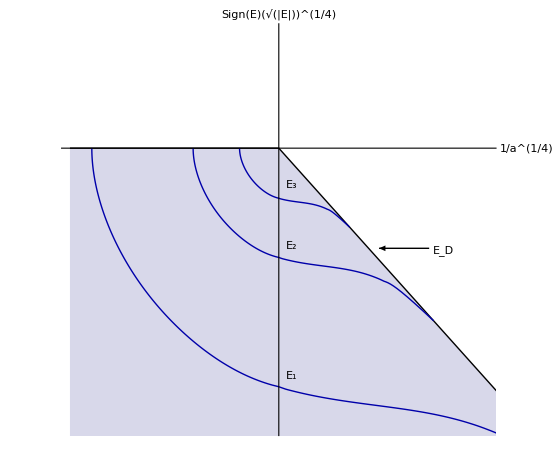

```mathematica
Show[Plot[threshold[x],{x,-1,30},PlotStyle->{Black},Filling->Bottom],Graphics[Text[Style["E_1",Medium],{0.06,-0.98}]],Graphics[Text[Style["E_2",Medium],{0.06,-0.42}]],Graphics[Text[Style["E_3",Medium],{0.06,-0.16}]],Graphics[{Arrow[{{0.72,-0.43},{0.48,-0.43}}],Text[Style["E_D",Medium],{0.79,-0.44}]}],ListLinePlot[{Effi,Effi1,Effi2},PlotStyle->{Darker[Blue],Darker[Blue],Darker[Blue]}],PlotRange->{{-1,1},{-1.2,0.5}},AxesStyle->Arrowheads[{0,0.036}],AxesLabel->{"1/a^(1/4)","Sign(E)(√(|E|))^(1/4)"},LabelStyle->Directive[Medium],Ticks->None,ImageSize->360,AspectRatio->Automatic]
```

```mathematica
Import["analytiskefimov/Borromean.png"]
```

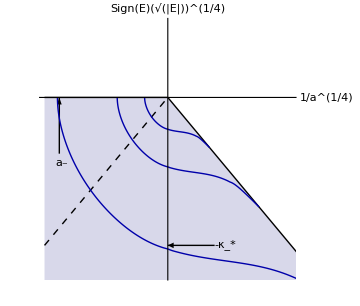

```mathematica
Show[Plot[threshold[x],{x,-1,30},PlotStyle->{Black},Filling->Bottom],Plot[threshold[-x],{x,-1,0},PlotStyle->{Black,Dashed}],Graphics[{Arrow[{{0.38,-1},{0,-1}}],Text[Style["-κ_*",Medium],{0.47,-1.03},{0.2,-0.5}]}],Graphics[{Arrow[{{-0.88,-0.38},{-0.88,0}}],Text[Style["a_-",Medium],{-0.86,-0.44},{0,-0.35}]}],ListLinePlot[{Effi,Effi1,Effi2},PlotStyle->{Darker[Blue],Darker[Blue],Darker[Blue]}],PlotRange->{{-1,1},{-1.2,0.5}},AxesStyle->Arrowheads[{0,0.036}],AxesLabel->{"1/a^(1/4)","Sign(E)(√(|E|))^(1/4)"},LabelStyle->Directive[Medium],Ticks->None,ImageSize->360,AspectRatio->Automatic]
```

```mathematica
GraphicsRow[{Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{-0.9,0},{0.9,0}}],Arrow[{{0,0},{0,1.67}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}]}],Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{0.94,0.1},{0.06,1.67}}],Arrow[{{0.5,0.866025},{-0.95,0.06}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}]}],Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{-0.06,1.67},{-0.95,0.1}}],Arrow[{{-0.5,0.866025},{0.95,0.06}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}]}]}]
```

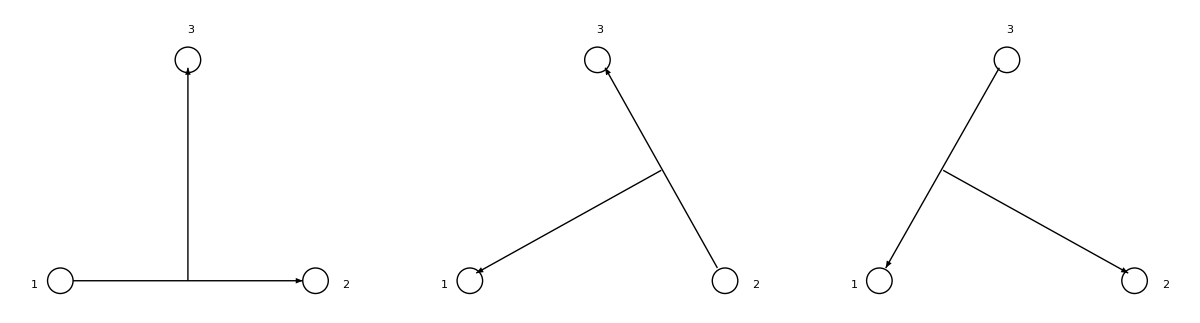

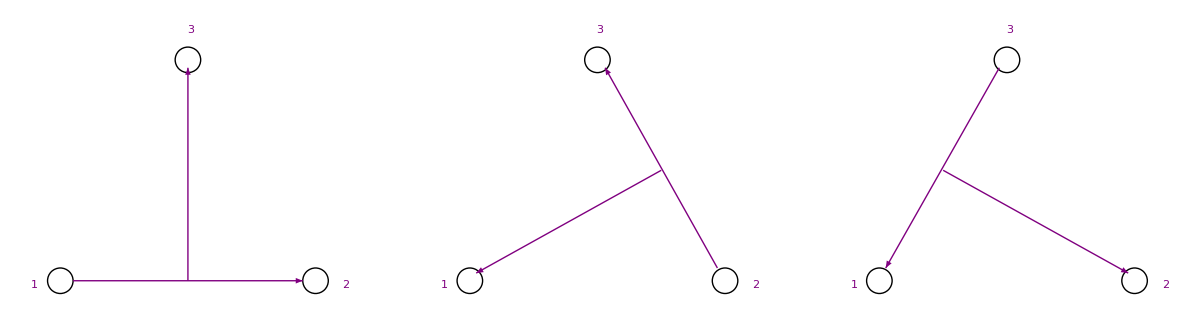

```mathematica
Text
```

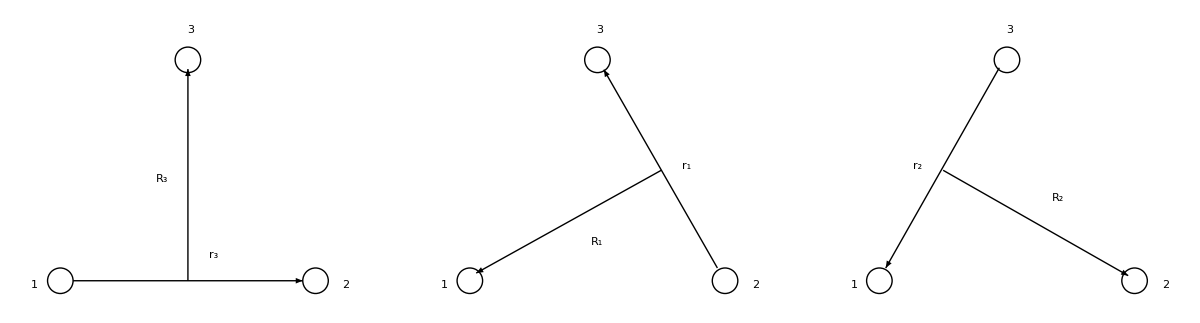

```mathematica
Show[GraphicsRow[{Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{-0.9,0},{0.9,0}}],Arrow[{{0,0},{0,1.66}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}],Text[Style[Subscript[Text[r], 3],Medium],{0.2,0.2}],Text[Style["R_3",Medium],{-0.2,0.8}]}],Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{0.94,0.1},{0.05,1.655}}],Arrow[{{0.5,0.866025},{-0.95,0.06}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}],Text[Style["r_1",Medium],{0.7,0.9}],Text[Style["R_1",Medium],{0,0.3}]}],Graphics[{Circle[{-1,0},0.1],Circle[{1,0},0.1],Circle[{0,1.73205},0.1],Arrowheads[Medium],Arrow[{{-0.06,1.67},{-0.95,0.1}}],Arrow[{{-0.5,0.866025},{0.95,0.04}}],Text[Style["1",Medium],{-1.2,-0.03}],Text[Style["2",Medium],{1.24,-0.03}],Text[Style["3",Medium],{0.02,1.97}],Text[Style["r_2",Medium],{-0.7,0.9}],Text[Style["R_2",Medium],{0.4,0.65}]}]}]]
```

```mathematica
■_□
```

```mathematica
Export["jacobii",%460,"EPS"]
```

jacobii

```mathematica
Export["jacobi",%434,"EPS"]
```

jacobi

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["jacobi"]]]
```

```mathematica
Export["jacobi",%423,"EPS"]
```

```mathematica
Import["analytiskefimov/Borromean.png"]
```

-Graphics-

image borromean ring

Import::nffil: File not found during Import.

$Failed

```mathematica
Imp
```

#### Wavefunction of an Efimov state

```mathematica
rmax=20000;
```

```mathematica
Clear[func,xi,fc,hypwfn,hypwfn1,hypwfn3]
```

```mathematica
func[xi_]:=NDSolve[{-fc''[x]+((Sqrt[Abs[lami[Abs[x H2[xi] Cos[xi]]]]]-1/4)/(x^2)+2*(H2[xi] Sin[xi])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]
```

```mathematica
func2[xi_]:=NDSolve[{-fc''[x]+((Sqrt[Abs[lami[Abs[x H[xi] Cos[xi]]]]]-1/4)/(x^2)+2*(H[xi] Sin[xi])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]
```

```mathematica
func1[xi_]:=NDSolve[{-fd''[x]+((Sqrt[Abs[lamdai[Abs[x H1[xi] Cos[xi]]]]]-1/4)/(x^2)+2*(H1[xi] Sin[xi])^2) fd[x]==0,fd[rmax]==0.0,fd'[rmax]==.01},fd,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]
```

```mathematica
hypwfn[x_,xi_]:=(fc[x]/x^(5/2))/.func[xi]⟦1⟧
```

```mathematica
hypwfn2[x_,xi_]:=(fc[x]/x^(5/2))/.func2[xi]⟦1⟧
```

```mathematica
hypwfn1[x_,xi_]:=(fd[x]/x^(5/2))/.func1[xi]⟦1⟧
```

```mathematica
hypwfn3[x_,xi_]:=Which[-π<=xi≤-π/2,hypwfn[x,xi],-π/2<xi≤-π/4,hypwfn1[x,xi]]
```

NDSolve::nlnum: The function value {0.01, -1.37772×10^-10\ (0.000302495  + 2.\ 0.00744679[-π/2]^2)} is not a list of numbers with dimensions {2} at xfc[x]SuperscriptBox[ = {50., -1.37772×10^-10, 0.01}.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nlnum: The function value {0.01, -1.37772×10^-10\ (0.000302495  + 2.\ 0.169242[-π/2]^2)} is not a list of numbers with dimensions {2} at xfd[x]SuperscriptBox[ = {50., -1.37772×10^-10, 0.01}.

General::stop: Further output of NDSolve :: nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

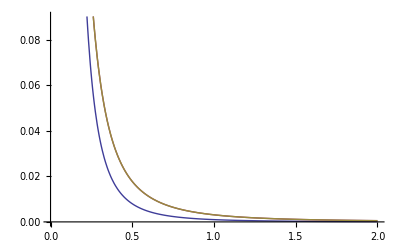

```mathematica
Plot[Evaluate[{hypwfn[x,-π/2]/hypwfn[0.1,-π/2],hypwfn2[x,-π/2]/hypwfn2[0.1,-π/2],hypwfn1[x,-π/2]/hypwfn1[0.1,-π/2]}],{x,0,2}]
```

```mathematica
norm=NIntegrate[hypwfn[r,-π/2]^2,{r, rmin,rmax}]
```

7.34538×10^49

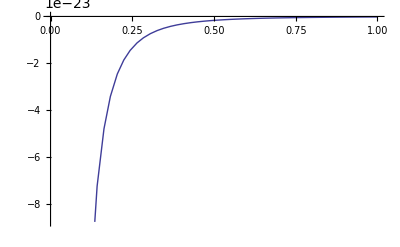

```mathematica
Plot[Evaluate[hypwfn[x,-π/2]/Sqrt[norm]],{x,rmin,1}]
```

```mathematica
Clear[x,α,ϕ,Totwfn]
```

```mathematica
x[r_,R_]:=(r^2/2+2 R^2/3)^(1/2)
```

```mathematica
α[r_,R_]:=ArcTan[√3 r/2 R]
```

```mathematica
ϕ[r_,R_]:=Sin[lami[Abs[x[r,R] H2[-π/2] Cos[-π/2]]] (α[r,R]-π/2)]
```

```mathematica
Totwfn[r_,R_]:=hypwfn[x[r,R],-π/2] ϕ[r,R]/(Sin[α[r,R]] Cos[α[r,R]])
```

```mathematica
Prob[r_]:=Totwfn[r,1]^2
```

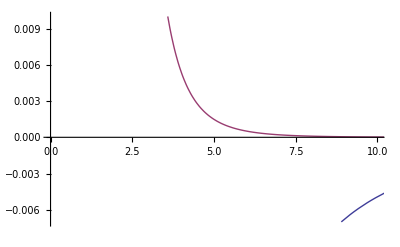

```mathematica
Plot[Evaluate[{Totwfn[r,1],Prob[r]}],{r,rmin,rmax},PlotRange->{{0,10},{-0.007,0.01}}]
```

### Comparing the experimental wavefunction with the analytically derived wavefunction for an Efimov state

Solving for H and Xi using the binding energy and the inverse scattering length

```mathematica
Clear[Xi,H,funccomp,hypwfncomp,ϕ,ϕ1,Compwfn,Ken,scatl,Bindingeng,kappasquared,ET,Xiii,v,Ken1,H1,ETex,X4]
```

```mathematica
v=1;

Bindingeng=0.02864291887533362;

scatl=-5955.87;

Xi=ArcTan[Bindingeng^(1/2) scatl]

kappasquared=(Bindingeng+1/scatl^2)/(Exp[gf[Xi]/s0])

ET[Xii_]:=(Tan[Xii]/scatl)^2

Xiii=FindRoot[(ET[Xii]+(1/scatl)^2)-(Exp[gf[Xii]/s0] kappasquared (Exp[-2 π/s0])^v)==0,{Xii,-π/2}]⟦1,2⟧
```

-1.5698

0.0285829

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-1.5708

```mathematica
Xiiii=FindRoot[(ET[Xiii]+(1/scatl)^2)-(Exp[gf[Xiii]/s0] kappasquared (Exp[-2 π/s0])^2)==0,{Xiii,-π/2}]⟦1,2⟧
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-1.5708

```mathematica
ETexx=Exp[gf[Xiiii]/s0] kappasquared (Exp[-2 π/s0])^2-(1/scatl)^2
```

7.95659×10^-8

```mathematica
Ken3=-Sqrt[ETexx]
```

-0.000282074

```mathematica
H4=Ken3/Sin[Xiiii]
```

0.000282074

```mathematica
kappasquared
```

0.0285752

```mathematica
n8=0;

X4=Xiii+n8 π

ETex=Exp[gf[X4]/s0] kappasquared (Exp[-2 π/s0])^v-(1/scatl)^2

Ken=-Sqrt[ETex];

H=Ken/Sin[X4];

Ken1=-Sqrt[Abs[Bindingeng]];

H1=Ken1/Sin[Xi];
H3=Exp[gf[Xi]/s0]*kappasquared/2;
Ken2=-H3*Sin[Xi];

funccomp:=NDSolve[{-fc''[x]+((lami[Abs[x H Cos[X4]]]-1/4)/(x^2)+2*(H Sin[X4])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]

hypwfncomp[x_]:=(fc[x]/x^(5/2))/.funccomp⟦1⟧

ϕ[r_,R_]:=Sin[Sqrt[Abs[lami[Abs[x[r,R] H Cos[X4]]]]] (α[r,R]-π/2)]

Compwfn[r_,R_]:=hypwfncomp[x[r,R]] ϕ[r,R]/(Sin[α[r,R]] Cos[α[r,R]])

funccomp1:=NDSolve[{-fc''[x]+(((lami[Abs[x H1 Cos[Xi]]]-1/4))/(x^2)+2*(H1 Sin[Xi])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]

hypwfncomp1[x_]:=(fc[x]/x^(5/2))/.funccomp1⟦1⟧

ϕ1[r_,R_]:=Sin[Sqrt[Abs[lami[Abs[x[r,R] H1 Cos[Xi]]]]] (α[r,R]-π/2)]
```

-1.5708

0.0000554696

```mathematica
Compwfn1[r_,R_]:=hypwfncomp1[x[r,R]] ϕ1[r,R]/(Sin[α[r,R]] Cos[α[r,R]])

funccomp2:=NDSolve[{-fc''[x]+((lami[Abs[x H3 Cos[Xi]]]-1/4)/(x^2)+2*(H3 Sin[Xi])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]
```

```mathematica
hypwfncomp2[x_]:=(fc[x]/x^(5/2))/.funccomp2⟦1⟧
```

```mathematica
ϕ2[r_,R_]:=Sin[Sqrt[Abs[lami[Abs[x[r,R] H3 Cos[Xi]]]]] (α[r,R]-π/2)]
```

```mathematica
Compwfn2[r_,R_]:=hypwfncomp2[x[r,R]] ϕ2[r,R]/(Sin[α[r,R]] Cos[α[r,R]])

funccomp3:=NDSolve[{-fc''[x]+((lami[Abs[x H4 Cos[Xiiii]]]-1/4)/(x^2)+2*(H3 Sin[Xiiii])^2) fc[x]==0,fc[rmax]==0.0,fc'[rmax]==.01},fc,{x,rmax,rmin},AccuracyGoal->14,MaxSteps->10000]
```

```mathematica
hypwfncomp3[x_]:=(fc[x]/x^(5/2))/.funccomp3⟦1⟧
```

```mathematica
ϕ3[r_,R_]:=Sin[Sqrt[Abs[lami[Abs[x[r,R] H4 Cos[Xiiii]]]]] (α[r,R]-π/2)]
```

```mathematica
Compwfn3[r_,R_]:=hypwfncomp1[x[r,R]] ϕ3[r,R]/(Sin[α[r,R]] Cos[α[r,R]])
```

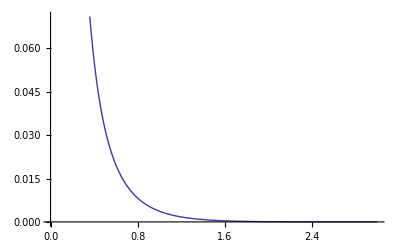

```mathematica
Plot[Evaluate[{(Compwfn[r,1])^2}],{r,rmin,3}]
```

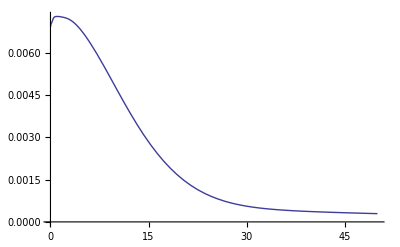

```mathematica
Plot[f[r,1],{r,rmin,rmax}]
```

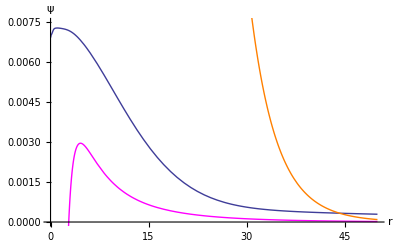

```mathematica
Show[Plot[f[r,1],{r,rmin,rmax}],Plot[Evaluate[{Compwfn[r,1],Compwfn1[r,1]}],{r,rmin,rmax},PlotStyle->{Magenta,Orange}],PlotRange->{{0,50},{0,0.0075}},AxesLabel->{"r","ψ"},LabelStyle->Directive[Medium]]
```

```mathematica
Plo
```

## Plotting the analytic efimov state using the numeric results

```mathematica
result=Import["/Users/kkm/Documents/Efimov_results.xlsx"];
```

```mathematica
re=result⟦1⟧//Grid
```

-5955.87 | -0.0286428
-1198.75 | -0.0281897
-665.314 | -0.0277388
-617.526 | -0.0269058
-546.938 | -0.0267678
-490.771 | -0.0266301
-416.884 | -0.0271411
-408.408 | -0.0263553
-303.945 | -0.0258082
-283.708 | -0.0263995
-214.688 | -0.0256643
-209.533 | -0.0248594
-159.552 | -0.0239214
-144.141 | -0.0242128
-121.824 | -0.0227316
-108.044 | -0.0227872
-98.3185 | -0.0215603
-86.1807 | -0.0213881
-63.5397 | -0.0184068
-53.0917 | -0.0173548
-49.2141 | -0.0159938
-34.5389 | -0.0123846
-28.7318 | -0.00939113
157.228 | -0.0332927
237.474 | -0.031719
343.794 | -0.0307861
404.453 | -0.030477
491.365 | -0.0301689
550.638 | -0.0300152
626.28 | -0.0298618
726.157 | -0.0297085
864.138 | -0.0295556
1067.17 | -0.0294028
1395.44 | -0.0292503
2016.53 | -0.0290981
3637.54 | -0.0289461
18641.7 | -0.0287943

#### Table Binding energy, scattering length and inverse scattering length

```mathematica
ree=First[re]
```

{{-5955.87,-0.0286428},{-1198.75,-0.0281897},{-665.314,-0.0277388},{-617.526,-0.0269058},{-546.938,-0.0267678},{-490.771,-0.0266301},{-416.884,-0.0271411},{-408.408,-0.0263553},{-303.945,-0.0258082},{-283.708,-0.0263995},{-214.688,-0.0256643},{-209.533,-0.0248594},{-159.552,-0.0239214},{-144.141,-0.0242128},{-121.824,-0.0227316},{-108.044,-0.0227872},{-98.3185,-0.0215603},{-86.1807,-0.0213881},{-63.5397,-0.0184068},{-53.0917,-0.0173548},{-49.2141,-0.0159938},{-34.5389,-0.0123846},{-28.7318,-0.00939113},{157.228,-0.0332927},{237.474,-0.031719},{343.794,-0.0307861},{404.453,-0.030477},{491.365,-0.0301689},{550.638,-0.0300152},{626.28,-0.0298618},{726.157,-0.0297085},{864.138,-0.0295556},{1067.17,-0.0294028},{1395.44,-0.0292503},{2016.53,-0.0290981},{3637.54,-0.0289461},{18641.7,-0.0287943}}

```mathematica
scaplo:=Table[{1/ree⟦i,1⟧,ree⟦i,2⟧},{i,Length[ree]}]


vdW=Import["/Users/kkm/Documents/vanderwaal.xlsx"];
vdw=vdW⟦1⟧//Grid
vdww=First[vdw]
test:=Table[{-(Abs[1/vdww⟦i,1⟧])^(1/4),-(Abs[vdww⟦i,2⟧])^(1/8)},{i,18}]
test2:=Table[{(Abs[1/vdww⟦i,1⟧])^(1/4),-(Abs[vdww⟦i,2⟧])^(1/8)},{i,19,32}]
test3:=Join[test,test2]
test3
```

122.3 | -15.3517 | -0.0651394 | -0.000127905
122.5 | -15.5004 | -0.0645145 | -0.000274032
123. | -15.8828 | -0.0629612 | -0.00064627
124. | -16.6972 | -0.0598903 | -0.0014203
125. | -17.5852 | -0.056866 | -0.00223344
126. | -18.5573 | -0.0538871 | -0.00308523
127. | -19.6261 | -0.0509526 | -0.00397509
135. | -34.5389 | -0.0289529 | -0.0123846
139. | -53.0917 | -0.0188353 | -0.0173548
142. | -86.1807 | -0.0116035 | -0.0213881
143. | -108.044 | -0.00925549 | -0.0227872
144. | -144.141 | -0.00693765 | -0.0242128
145. | -214.688 | -0.00465792 | -0.0256643
145.5 | -283.708 | -0.00352475 | -0.0263995
146. | -416.884 | -0.00239875 | -0.0271411
146.4 | -665.314 | -0.00150305 | -0.0277388
146.7 | -1198.75 | -0.000834202 | -0.0281897
147. | -5955.87 | -0.000167902 | -0.0286428
147.1 | 18641.7 | 0.0000536432 | -0.0287943
147.2 | 3637.54 | 0.000274911 | -0.0289461
147.3 | 2016.53 | 0.000495901 | -0.0290981
147.4 | 1395.44 | 0.00071662 | -0.0292503
147.5 | 1067.17 | 0.000937058 | -0.0294028
147.6 | 864.138 | 0.00115722 | -0.0295556
147.7 | 726.157 | 0.00137711 | -0.0297085
147.8 | 626.28 | 0.00159673 | -0.0298618
147.9 | 550.638 | 0.00181608 | -0.0300152
148. | 491.365 | 0.00203515 | -0.0301689
148.2 | 404.453 | 0.00247248 | -0.030477
148.4 | 343.794 | 0.00290872 | -0.0307861
149. | 237.474 | 0.00421099 | -0.031719
150. | 157.228 | 0.00636019 | -0.0332927

{{122.3,-15.3517,-0.0651394,-0.000127905},{122.5,-15.5004,-0.0645145,-0.000274032},{123.,-15.8828,-0.0629612,-0.00064627},{124.,-16.6972,-0.0598903,-0.0014203},{125.,-17.5852,-0.056866,-0.00223344},{126.,-18.5573,-0.0538871,-0.00308523},{127.,-19.6261,-0.0509526,-0.00397509},{135.,-34.5389,-0.0289529,-0.0123846},{139.,-53.0917,-0.0188353,-0.0173548},{142.,-86.1807,-0.0116035,-0.0213881},{143.,-108.044,-0.00925549,-0.0227872},{144.,-144.141,-0.00693765,-0.0242128},{145.,-214.688,-0.00465792,-0.0256643},{145.5,-283.708,-0.00352475,-0.0263995},{146.,-416.884,-0.00239875,-0.0271411},{146.4,-665.314,-0.00150305,-0.0277388},{146.7,-1198.75,-0.000834202,-0.0281897},{147.,-5955.87,-0.000167902,-0.0286428},{147.1,18641.7,0.0000536432,-0.0287943},{147.2,3637.54,0.000274911,-0.0289461},{147.3,2016.53,0.000495901,-0.0290981},{147.4,1395.44,0.00071662,-0.0292503},{147.5,1067.17,0.000937058,-0.0294028},{147.6,864.138,0.00115722,-0.0295556},{147.7,726.157,0.00137711,-0.0297085},{147.8,626.28,0.00159673,-0.0298618},{147.9,550.638,0.00181608,-0.0300152},{148.,491.365,0.00203515,-0.0301689},{148.2,404.453,0.00247248,-0.030477},{148.4,343.794,0.00290872,-0.0307861},{149.,237.474,0.00421099,-0.031719},{150.,157.228,0.00636019,-0.0332927}}

{{-0.300707,-1.40692},{-0.300584,-1.40862},{-0.300278,-1.41291},{-0.299671,-1.42177},{-0.29907,-1.43101},{-0.298475,-1.44067},{-0.297885,-1.45079},{-0.293371,-1.557},{-0.291237,-1.64297},{-0.289686,-1.74553},{-0.289178,-1.79556},{-0.288675,-1.86144},{-0.288176,-1.95648},{-0.287928,-2.02586},{-0.287681,-2.1257},{-0.287485,-2.25361},{-0.287338,-2.42572},{-0.287191,-2.96393},{0.287142,-3.4183},{0.287093,-2.78677},{0.287045,-2.58866},{0.286996,-2.47223},{0.286947,-2.39072},{0.286899,-2.32848},{0.28685,-2.27839},{0.286801,-2.23664},{0.286753,-2.20094},{0.286705,-2.16983},{0.286608,-2.11767},{0.286511,-2.07509},{0.286222,-1.98131},{0.285744,-1.88177}}

```mathematica
ListPlot[%1371,AxesLabel->{"1/a^(1/4)","Sign(E)|E|^(1/8)"},LabelStyle->Directive[Medium],PlotRange->{{-0.57,0.3},{-0.67,-0.3}}]
```

-Graphics-

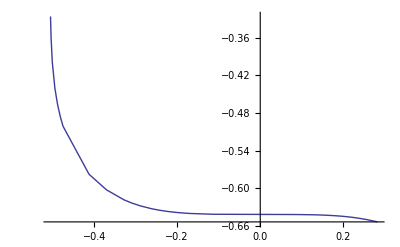

```mathematica
ListPlot[%1346,Joined->True]
```

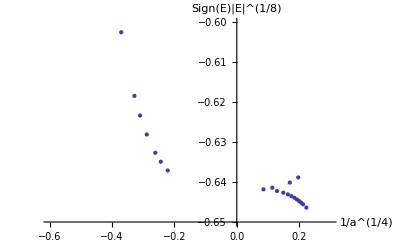

```mathematica
ListPlot[%1280,AxesLabel->{"1/a^(1/4)","Sign(E)|E|^(1/8)"},LabelStyle->Directive[Medium],PlotRange->{{-0.6,0.3},{-0.65,-0.6}}]
```

```mathematica
ListPlot[%1217,AxesLabel->{"1/a^(1/4)","Sign(E)|E|^(1/8)"},LabelStyle->Directive[Medium],PlotRange->{{-0.6,0.3},{-0.65,-0.6}}]
```

-Graphics-

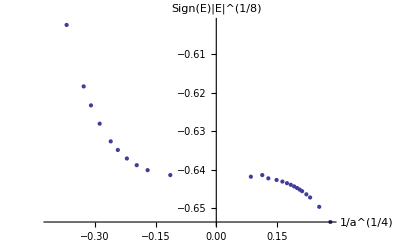

```mathematica
ListPlot[%1075,AxesLabel->{"1/a^(1/4)","Sign(E)|E|^(1/8)"},LabelStyle->Directive[Medium]]
```

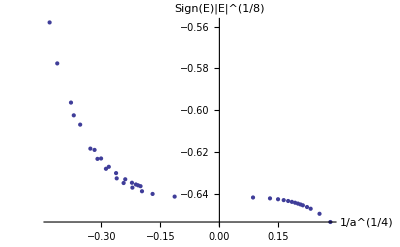

```mathematica
ListPlot[%1005,AxesLabel->{"1/a^(1/4)","Sign(E)|E|^(1/8)"},LabelStyle->Directive[Medium]]
```

```mathematica
ree2b=First[re2b];
scalplot2b:=Table[{1/ree2b⟦i,1⟧,ree2b⟦i,2⟧},{i,Length[ree2b]}]
```

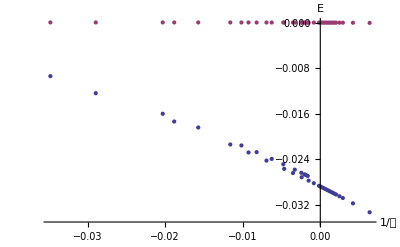

```mathematica
ListPlot[{scaplo,scalplot2b},AxesOrigin->{0,-0.035}, AxesLabel->{"1/𝒶","E"},LabelStyle->Directive[Medium]]
```

```mathematica
Axe
```

#### Table Xi,Kappasquared

```mathematica
kappasquared=(Bindingeng+1/scatl^2)/(Exp[gf[Xi]/s0])
```

```mathematica
N[π/2]
```

1.5708

```mathematica
Arc
```

0.0285752

```mathematica
s0
```

1.006240000000000023305802

```mathematica
res:=Table[{ArcTan[1/ree⟦i,1⟧,-(Abs[ree⟦i,2⟧])^(1/2) ],(Abs[ree⟦i,2⟧]+1/(ree⟦i,1⟧)^2)/Exp[gf[ArcTan[1/ree⟦i,1⟧,-(Abs[ree⟦i,2⟧])^(1/2) ]]/s0]},{i,Length[ree]}]
```

```mathematica
res
```

{{-1.57179,0.0287029},{-1.57576,0.0284866},{-1.57982,0.0282709},{-1.58067,0.0274707},{-1.58197,0.0274045},{-1.58328,0.0273385},{-1.58536,0.0279842},{-1.58588,0.0272036},{-1.59127,0.0269402},{-1.59249,0.0276271},{-1.59986,0.0272716},{-1.60106,0.0264815},{-1.6113,0.0260254},{-1.61535,0.0265622},{-1.62519,0.0254425},{-1.63203,0.0258615},{-1.63995,0.0248637},{-1.64997,0.0251665},{-1.68628,0.0232755},{-1.71281,0.0231116},{-1.7301,0.0220234},{-1.82532,0.0204305},{-1.9156,0.0183335},{-1.53595,0.0308979},{-1.54716,0.0301596},{-1.55422,0.0297198},{-1.55663,0.0295737},{-1.55908,0.029428},{-1.56031,0.0293552},{-1.56156,0.0292825},{-1.56281,0.0292097},{-1.56407,0.0291372},{-1.56533,0.0290646},{-1.56661,0.0289921},{-1.56789,0.0289197},{-1.56918,0.0288474},{-1.57048,0.0287751}}

```mathematica
N[Sqrt[0.0199682]]
```

0.141309

```mathematica
N[Sqrt[0.0287]^(1/4)]
```

0.641557

```mathematica
Hres:=Table[Sqrt[Abs[Exp[gf[res⟦i,1⟧]/s0]*res⟦i,2⟧]],{i,Length[res]}]
```

```mathematica
HHres10:=Table[{(Abs[Hres⟦i⟧]) Cos[res⟦i,1⟧],(Abs[Hres⟦i⟧]) Sin[res⟦i,1⟧]},{i,Length[Hres]}]
```

```mathematica
HHres10
```

{{-0.000167902,-0.169242},{-0.000834202,-0.167898},{-0.00150305,-0.16655},{-0.00161937,-0.16403},{-0.00182836,-0.163609},{-0.00203761,-0.163187},{-0.00239875,-0.164746},{-0.00244853,-0.162343},{-0.00329007,-0.160649},{-0.00352475,-0.162479},{-0.00465792,-0.160201},{-0.00477252,-0.157669},{-0.00626755,-0.154665},{-0.00693765,-0.155605},{-0.00820856,-0.15077},{-0.00925549,-0.150954},{-0.010171,-0.146834},{-0.0116035,-0.146247},{-0.0157382,-0.135672},{-0.0188353,-0.131738},{-0.0203194,-0.126467},{-0.0289529,-0.111286},{-0.0348046,-0.0969078},{0.00636019,-0.182463},{0.00421099,-0.178098},{0.00290872,-0.17546},{0.00247248,-0.174577},{0.00203515,-0.173692},{0.00181608,-0.173249},{0.00159673,-0.172806},{0.00137711,-0.172362},{0.00115722,-0.171917},{0.000937058,-0.171472},{0.00071662,-0.171027},{0.000495901,-0.170582},{0.000274911,-0.170136},{0.0000536432,-0.169689}}

```mathematica
Xiii=FindRoot[(ET[Xii]+(1/scatl)^2)-(Exp[gf[Xii]/s0] kappasquared (Exp[-2 π/s0])^v)==0,{Xii,-π/1.5}]⟦1,2⟧
```

InterpolatingFunction::dmval: Input value {-0.385716} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {33.4539} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-37.6991

```mathematica
Sqrt[0.03]
```

0.173205

#### Table Xiii

```mathematica
res3:=Table[FindRoot[((Tan[Xii]/ree⟦i,1⟧)^2+(1/ree⟦i,1⟧)^2)-(Exp[gf[Xii]/s0]*res⟦i,2⟧*(Exp[-2 π/s0])^1)==0,{Xii,-π/1.9}]⟦1,2⟧,{i,23}]
```

```mathematica
res3
```

InterpolatingFunction::dmval: Input value {1.67908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.14495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{-1.59383,-1.69766,-1.82581,-1.85585,-1.90443,-1.95636,-2.04504,-2.06865,-2.34395,-2.41368,-2.93123,-3.14135,-3.14141,-3.14143,-1.06884,-3.14149,-3.14151,-3.14152,-3.14155,-3.14157,-3.14157,-3.14158,-3.14159}

```mathematica
res4:=Table[FindRoot[((Tan[Xii]/ree⟦i,1⟧)^2+(1/ree⟦i,1⟧)^2)-(Exp[gf[Xii]/s0/2] res⟦i,2⟧ (Exp[-2 π/s0])^1)==0,{Xii,-π/4}]⟦1,2⟧,{i,24,36}]
```

```mathematica
res4
```

{-1.04126,-1.16092,-1.25868,-1.2966,-1.3375,-1.35912,-1.38156,-1.40485,-1.42899,-1.45403,-1.67125,-1.63933,-1.53477}

```mathematica
res5:=Join[res3,res4]
```

```mathematica
res5
```

InterpolatingFunction::dmval: Input value {1.67908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.14495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{-1.59383,-1.69766,-1.82581,-1.85585,-1.90443,-1.95636,-2.04504,-2.06865,-2.34395,-2.41368,-2.93123,-3.14135,-3.14141,-3.14143,-1.06884,-3.14149,-3.14151,-3.14152,-3.14155,-3.14157,-3.14157,-3.14158,-3.14159,-1.02562,-1.14581,-1.24562,-1.28466,-1.32693,-1.34935,-1.37267,-1.3969,-1.42208,-1.44824,-1.67689,-1.64312,-1.61029}

```mathematica
ETex=Exp[gf[X4]/s0] kappasquared (Exp[-2 π/s0])^v-(1/scatl)^2

Ken=-Sqrt[ETex];
```

```mathematica
H=Ken/Sin[X4];
```

#### Table H

```mathematica
(Exp[2 π/s0])^(n-n0) Exp[gf[ξ]/s0]
```

```mathematica
res8:=Table[Sqrt[Abs[Exp[gf[res5⟦i⟧]/s0] res⟦i,2⟧ (Exp[-2 π/s0])^0]],{i,Length[res5]}]
```

```mathematica
res9:=Table[Sqrt[Abs[Exp[gf[res5⟦i⟧]/s0] res⟦i,2⟧ (Exp[-2 π/s0])^1]],{i,Length[res5]}]
```

```mathematica
res15:=Table[{(Abs[res9⟦i⟧])^(1/4) Cos[res5⟦i⟧],(Abs[res9⟦i⟧])^(1/4) Sin[res5⟦i⟧]},{i,Length[res9]}]
```

```mathematica
res15
```

InterpolatingFunction::dmval: Input value {1.67908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.14495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-0.0067304,-0.292117},{-0.0360528,-0.282666},{-0.0700845,-0.268848},{-0.0774664,-0.264355},{-0.0895164,-0.258278},{-0.102034,-0.251388},{-0.12294,-0.239503},{-0.127787,-0.235108},{-0.18297,-0.187504},{-0.195696,-0.174399},{-0.256914,-0.0548557},{-0.262829,-0.000064689},{-0.262259,-0.0000476633},{-0.262929,-0.0000424839},{0.17389,-0.316825},{-0.262052,-0.0000277049},{-0.260766,-0.0000228315},{-0.261161,-0.0000186768},{-0.258624,-0.0000100987},{-0.258395,-6.86244×10^-6},{-0.256842,-5.77692×10^-6},{-0.254443,-3.00545×10^-6},{-0.251022,-1.71684×10^-6},{0.191062,-0.326439},{0.138501,-0.318774},{0.101233,-0.313739},{0.0876972,-0.311776},{0.0735639,-0.309579},{0.0662666,-0.308371},{0.0588123,-0.307076},{0.0511993,-0.305685},{0.0434254,-0.304185},{0.0354895,-0.302564},{-0.028804,-0.285778},{-0.0198061,-0.288559},{0.0106986,-0.296835}}

#### Table Hcos(Xiii),Hsin(Xiii)

```mathematica
res7:=Table[{(Abs[res8⟦i⟧])^(1/4) Cos[res5⟦i⟧],(Abs[res8⟦i⟧])^(1/4) Sin[res5⟦i⟧]},{i,Length[res8]}]
```

```mathematica
res7
```

InterpolatingFunction::dmval: Input value {1.67908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.14495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-0.0146899,-0.63758},{-0.0786897,-0.616953},{-0.152968,-0.586794},{-0.16908,-0.576988},{-0.195381,-0.563723},{-0.222702,-0.548685},{-0.268332,-0.522745},{-0.278911,-0.513153},{-0.399354,-0.409251},{-0.42713,-0.380647},{-0.560746,-0.119729},{-0.573657,-0.000141192},{-0.572413,-0.000104031},{-0.573875,-0.0000927264},{0.379536,-0.69151},{-0.571961,-0.0000604694},{-0.569155,-0.0000498327},{-0.570017,-0.0000407644},{-0.564478,-0.0000220417},{-0.56398,-0.0000149781},{-0.56059,-0.0000126088},{-0.555354,-6.55976×10^-6},{-0.547886,-3.74722×10^-6},{0.417017,-0.712494},{0.302295,-0.695765},{0.220954,-0.684773},{0.19141,-0.680489},{0.160562,-0.675694},{0.144635,-0.673057},{0.128365,-0.670232},{0.111749,-0.667194},{0.0947814,-0.663921},{0.0774601,-0.660382},{-0.0628683,-0.623746},{-0.0432293,-0.629816},{0.023351,-0.647879}}

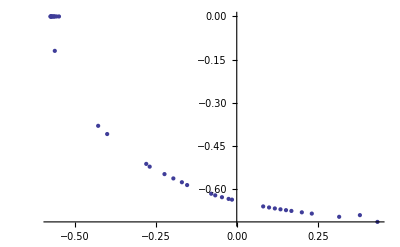

```mathematica
ListPlot[%2180]
```

```mathematica
res11:=Table[Sqrt[Abs[Exp[gf[res5⟦i⟧]/s0] res⟦i,2⟧ (Exp[-2 π/s0])^2]],{i,Length[res5]}]
```

```mathematica
res12:=Table[{(Abs[res11⟦i⟧])^(1/4) Cos[res5⟦i⟧],(Abs[res11⟦i⟧])^(1/4) Sin[res5⟦i⟧]},{i,Length[res11]}]
```

```mathematica
res12
```

InterpolatingFunction::dmval: Input value {1.67908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.745926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.14495} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-0.00308363,-0.133837},{-0.0165181,-0.129507},{-0.0321102,-0.123177},{-0.0354923,-0.121118},{-0.0410132,-0.118334},{-0.0467483,-0.115177},{-0.0563267,-0.109732},{-0.0585475,-0.107718},{-0.0838301,-0.0859078},{-0.0896608,-0.0799032},{-0.117709,-0.0251329},{-0.120419,-0.0000296382},{-0.120158,-0.0000218376},{-0.120465,-0.0000194646},{0.07967,-0.145158},{-0.120063,-0.0000126934},{-0.119474,-0.0000104606},{-0.119655,-8.55704×10^-6},{-0.118492,-4.62687×10^-6},{-0.118387,-3.14413×10^-6},{-0.117676,-2.64678×10^-6},{-0.116577,-1.37699×10^-6},{-0.115009,-7.86595×10^-7},{0.0875379,-0.149563},{0.0634561,-0.146051},{0.0463814,-0.143744},{0.0401797,-0.142845},{0.0337043,-0.141838},{0.030361,-0.141284},{0.0269457,-0.140691},{0.0234577,-0.140054},{0.019896,-0.139367},{0.01626,-0.138624},{-0.013197,-0.130933},{-0.00907445,-0.132207},{0.00490171,-0.135999}}

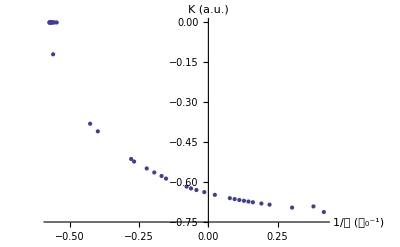

```mathematica
ListPlot[%1612,Axes->True,AxesOrigin->{0,-0.75},AxesLabel->{"1/𝒶 (𝒶_0^-1)","K (a.u.)"},LabelStyle->{Directive[Medium]}]
```

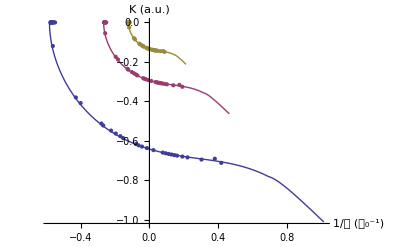

```mathematica
Show[ListLinePlot[{Effi,Effi1, Effi2}],ListPlot[{%1612,%1619,%1617}],Axes->True,AxesOrigin->{0,-1.02},AxesLabel->{"1/𝒶 (𝒶_0^-1)","K (a.u.)"},LabelStyle->Directive[Medium]]
```

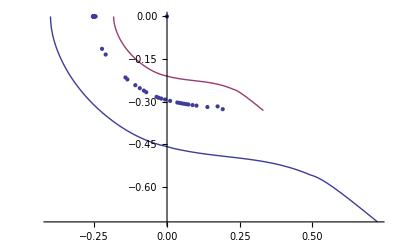

```mathematica
Show[ListLinePlot[{Effi1,Effi2}],ListPlot[%902]]
```

#### Table Xii, Xiii, Kappasquared, H

```mathematica
resultt:=Table[{res⟦i,1⟧,res5⟦i⟧,res⟦i,2⟧,res9⟦i⟧},{i,Length[res]}]
```

```mathematica
resultt
```

InterpolatingFunction::dmval: Input value {2.15726} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.16832} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-1.57179,-1.59375,0.0286994,0.166022},{-1.57576,-1.69677,0.028463,0.150681},{-1.57982,-1.83213,0.0282177,0.132021},{-1.58067,-1.86666,0.027412,0.126042},{-1.58197,-1.92564,0.0273346,0.119426},{-1.58328,-1.99356,0.0272567,0.112708},{-1.58536,-2.12133,0.0278796,0.10406},{-1.58588,-2.15742,0.0270967,0.100383},{-1.59127,-2.57511,0.0267764,0.0884879},{-1.59249,-2.66939,0.0274449,0.0898207},{-1.59986,-3.14132,0.0270058,0.0958424},{-1.60106,-3.14133,0.02621,0.0944199},{-1.6113,-3.14139,0.025692,0.0934821},{-1.61535,-3.14141,0.026201,0.0944037},{-1.62519,-1.06871,0.025057,0.387086},{-1.63203,-3.14147,0.0254489,0.0930389},{-1.63995,-3.14149,0.024451,0.0911965},{-1.64997,-3.14151,0.0247387,0.0917315},{-1.68628,-3.14154,0.0229307,0.0883158},{-1.71281,-3.14156,0.0228816,0.0882211},{-1.7301,-3.14156,0.0219032,0.0863144},{-1.82532,-3.14158,0.0211367,0.0847907},{-1.9156,-3.14158,0.0199682,0.0824137},{-1.53595,-1.04014,0.0304532,0.466098},{-1.54716,-1.16044,0.0298479,0.332151},{-1.55422,-1.25871,0.0295186,0.269011},{-1.55663,-1.29676,0.0294088,0.250693},{-1.55908,-1.33776,0.0292981,0.233681},{-1.56031,-1.35942,0.0292423,0.225653},{-1.56156,-1.38188,0.029186,0.217935},{-1.56281,-1.40517,0.0291291,0.210523},{-1.56407,-1.42931,0.0290718,0.20341},{-1.56533,-1.45432,0.0290136,0.19659},{-1.56661,-1.67088,0.0289547,0.155692},{-1.56789,-1.63906,0.0288951,0.160133},{-1.56918,-1.53489,0.0288344,0.177876},{-1.57048,-6.28319,0.0287727,3.51931×10^-26}}

```mathematica
vander1=Import["/Users/kkm/Documents/newvanderwaal.xlsx"];
```

```mathematica
va1=vander1⟦1⟧//Grid
```

-0.0651394 | -0.000128
-0.0645145 | -0.000274
-0.0629612 | -0.000646
-0.0598903 | -0.00142
-0.056866 | -0.00223
-0.0538872 | -0.00309
-0.0509526 | -0.00398
-0.0289529 | -0.0123846
-0.0188353 | -0.0173548
-0.0116035 | -0.0213881
-0.00925549 | -0.0227872
-0.00693765 | -0.0242128
-0.00465792 | -0.0256643
-0.00352475 | -0.0263995
-0.00239875 | -0.0271411
-0.00150305 | -0.0277388
-0.000834202 | -0.0281897
-0.000167902 | -0.0286428
0.0000536432 | -0.0287943
0.000274911 | -0.0289461
0.000495901 | -0.0290981
0.00071662 | -0.0292503
0.000937058 | -0.0294028
0.00115722 | -0.0295556
0.00137711 | -0.0297085
0.00159673 | -0.0298618
0.00181608 | -0.0300152
0.00203515 | -0.0301689
0.00247248 | -0.030477
0.00290872 | -0.0307861
0.00421099 | -0.031719
0.00636019 | -0.0332927

```mathematica
vaa1=First[va1];
```

```mathematica
vas1:=Table[{ArcTan[vaa1⟦i,1⟧,-(Abs[vaa1⟦i,2⟧])^(1/2) ],(Abs[vaa1⟦i,2⟧]+(vaa1⟦i,1⟧)^2)/Exp[gf[ArcTan[vaa1⟦i,1⟧,-(Abs[vaa1⟦i,2⟧])^(1/2) ]]/s0]},{i,Length[vaa1]}]
```

```mathematica
vass:=Table[FindRoot[((Tan[Xii]/vaa1⟦i,1⟧)^2+(vaa1⟦i,1⟧)^2)-(Exp[gf[Xii]/s0/2] vas1⟦i,2⟧ (Exp[-2 π/s0])^1)==0,{Xii,-π/4}]⟦1,2⟧,{i,19,32}]
```

```mathematica
vass
```

InterpolatingFunction::dmval: Input value {-0.535398} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.760398} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{-0.644599,-0.653562,-0.657001,-0.65921,-0.660852,-0.662165,-0.663261,-0.664204,-0.665033,-0.665773,-0.667052,-0.668135,-0.670656,-0.673574}

```mathematica
N[π/4]
```

0.785398

```mathematica
vas2:=Table[FindRoot[((Tan[Xii] vaa1⟦i,1⟧)^2+(1 vaa1⟦i,1⟧)^2)-(Exp[gf[Xii]/s0]*vas1⟦18,2⟧*(Exp[-2 π/s0])^1)==0,{Xii,-π/1.8}]⟦1,2⟧,{i,Length[vaa1]}]
```

```mathematica
vas2
```

InterpolatingFunction::dmval: Input value {-3.22635} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14157,-3.14155,-3.1415,-1.05785,-3.1414,-3.14131,-2.63162,-2.10709,-1.82914,-1.69618,-4.15955,-4.28262,-9.42478,-1.64153,-1.67646,-1.71416,-1.75529,-1.80073,-1.85159,-1.90923,-1.97524,-2.13736,-2.33522,-2.97757,-3.14138}

```mathematica
vas3:=Table[Sqrt[Abs[Exp[gf[vas2⟦i⟧]/s0] vas1⟦18,2⟧ (Exp[-2 π/s0])^0]],{i,Length[vaa1]}]
```

```mathematica
vas4:=Table[{((Abs[vas3⟦i⟧]^(1/4)) Cos[vas2⟦i⟧]),(Abs[vas3⟦i⟧]^(1/4)) Sin[vas2⟦i⟧]},{i,Length[vas1]}]
```

```mathematica
vas4
```

InterpolatingFunction::dmval: Input value {-3.4352} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{-0.56065,-2.00122×10^-6},{-0.56065,-2.69537×10^-6},{-0.56065,-2.16375×10^-6},{-0.56065,-3.03723×10^-6},{-0.56065,-3.39441×10^-6},{-0.56065,-2.58516×10^-6},{-0.56065,-3.92023×10^-6},{-0.56065,-0.0000103291},{-0.56065,-0.0000237908},{-0.56065,-0.0000546325},{0.396937,-0.704747},{-0.56065,-0.000109439},{-0.56065,-0.000157948},{-0.480211,-0.268591},{-0.291919,-0.49111},{-0.154433,-0.584421},{-0.0780035,-0.618873},{-0.0146503,-0.638156},{-0.0968715,0.211351},{-0.024214,-0.635866},{-0.0446462,-0.630117},{-0.0660896,-0.623153},{-0.0887405,-0.614764},{-0.112843,-0.604671},{-0.138692,-0.592508},{-0.16664,-0.577793},{-0.197072,-0.559904},{-0.230326,-0.538092},{-0.305199,-0.479772},{-0.384629,-0.40111},{-0.550394,-0.0910951},{-0.56065,-0.000119946}}

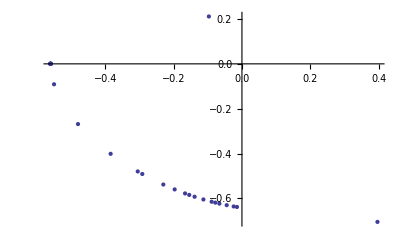

```mathematica
ListPlot[%1694]
```

```mathematica
(0.64*1.662)*(-9.23)
```

-9.81777

```mathematica
0.64*1.662
```

1.06368

```mathematica
0.64*1.741298286
```

1.11443

```mathematica
Sqrt[0.0287943]
```

0.169689

```mathematica
0.17*(-15.23)
```

-2.5891

```mathematica
Sqrt[0.0286994]
```

```mathematica
0.16940897260771048*1.741002273
```

```mathematica
0.2949414063766187*-9.232724068
```

-2.72311

```mathematica
N[π/2]
```

1.5708

```mathematica
Integrate[x*(Sin[x]/(1 + x^2)), x]
```

-(-ⅈ (-1+ⅇ^2) CosIntegral[ⅈ-x]+ⅈ (-1+ⅇ^2) CosIntegral[ⅈ+x]+(1+ⅇ^2) (SinIntegral[ⅈ-x]-SinIntegral[ⅈ+x]))/(4 ⅇ)

```mathematica
Clear[s]
```

```mathematica
s=∫_(-∞)^∞ x*(Sin[x]/( x-2))ⅆx
```

Integrate::idiv: Integral of x\ Sin[x]/-2 + x does not converge on {-∞, ∞}.

∫_(-∞)^∞ (x Sin[x])/(-2+x)ⅆx

```mathematica
N[-(ⅇ^2 ExpIntegralEi[-1]+ExpIntegralEi[1])/(2 ⅇ)]
```

-0.0504138

```mathematica
N[(ⅇ^2 ExpIntegralEi[-1]+ExpIntegralEi[1])/(2 ⅇ)]
```

0.0504138

```mathematica
Cosh[0]
```

1